Info on the notebook:
This notebook uses the BiGONLight package to compute observables in conformal EdS model.
It is structured as follows: 
- model set-up:  give the 4D metric tensor components as input and compute the 3+1 quantities lapse α, shift β^i, spatial metric γ_ij, extrinsic curvature K_ij and the normal vector n^μ;
- geodesic: provide initial position and tangent vector {x^μ, ℓ^μ} as input to find null geodesics;
- parallel transported frame: give the initial conditions for a frame (ϕ^μ)_αthat will be parallel transported along the computed geodesic (we use the SNF, i.e. (ϕ^μ)_α={u^μ,(ϕ^μ)_1,(ϕ^μ)_2, ℓ^μ} with u^μ the four-velocity and (ϕ^μ)_A two orthonormal vectors)
- optical tidal matrix: compute the optical tidal matrix (R^μ)_ρσν ℓ^ρ ℓ^σ in the parallel propagated frame; 
- BGO: compute and solve the Geodesic Deviation Equation for the Bi-local Geodesic Operators along the null geodesic;
- observables: compute the optical observables in the BGO framework: redshift, redshift drift, angular diameter distance, luminosity distance, parallax distance, distance slip, convergence and shear.

Set the current directory as working directory and load the package.

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["bigonlight`"]
```

```mathematica
prec=16
$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`16."&);(*MachinePrecision:>s<>"`prec."&*)
```

16

a generic direction can be written as 𝓋^μ=𝓋^0∂_0 +γ(sinχ cosξ ∂_1 +sinχ sinξ ∂_1 +cosχ ∂_3)=(𝓋^0(∂_0))^μ+γ (N⃗)^μ with respect to the local tetrad ∂_μ . 
In particular for a null direction 𝓋^0=±1 and γ=1 , while for a timelike direction 𝓋^0=±c γ and ψ=c γ β  where β=vel/c the normalized velocity and γ=1/(√(1-β^2)) the Lorentz factor.
import data on files
BGO=<<”BGO_data.m”;
totN=<<”geodesic_data.m”;

```mathematica
𝒱[Vt_,lorentz_,direction1_,direction2_]:=
Module[{V0=Vt, γ=lorentz,χ=direction1,ξ=direction2},
V0{1,0,0,0}+γ(Sin[χ]Cos[ξ]{0,1,0,0}+Sin[χ]Sin[ξ]{0,0,1,0}+Cos[χ]{0,0,0,1})
]

StandardPlotStyle[size_,sizelegend_,ylabel_,xlabel_,title_,legend_,position_]:=Module[{ft=size,ftL=sizelegend,yL=ylabel,xL=xlabel,pt=title,list=legend,pl=position},
If[ list=={},{FrameLabel->{{yL,""},{xL,""}},Frame->True,FrameTicks->True,FrameStyle->Directive[FontSize->ft],GridLines->Automatic,GridLinesStyle->Directive[Gray,Opacity[0.2],Dashed],PlotLabel->Style[pt,Bold,FontSize->ft]},{FrameLabel->{{yL,""},{xL,""}},Frame->True,FrameTicks->True,FrameStyle->Directive[FontSize->ft],GridLines->Automatic,GridLinesStyle->Directive[Gray,Opacity[0.2],Dashed],PlotLabel->Style[pt,Bold,FontSize->ft],PlotLegends->Placed[LineLegend[Table[Style[list[[m]],FontSize->ftL],{m,1,Length[list]}]],pl]},Print["Error"]]];
```

# FLRWSolver

## Import data from spacetime simulation

```mathematica
iℋ=SetPrecision[Take[Cases[Import["Data_FLRWSolver/res_0.05/H.average.asc","Table"],{__?NumericQ}],All,-2],prec];
```

```mathematica
Do[If[iℋ[[i,2]]> 10^-8,rel=i-1;Print[ToString[ {i,iℋ[[i,1]],iℋ[[i,2]]}]];Break[],rel=i-1],{i,1,Length@iℋ}]
```

```mathematica
(*iℋ[[3119,2]]*)
iℋ[[rel,2]]
rel
```

-5.64689403538105×10^-18

64400

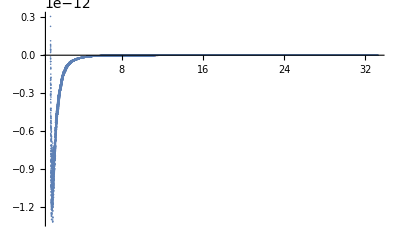

```mathematica
ListPlot[Table[iℋ[[i]],{i,1,rel}],PlotRange->All]
```

```mathematica
iα=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/alp.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
```

```mathematica
iα[[Length@iα]]
iℋ[[rel]]
```

{33.1995,1102.20680013852}

{33.1995,-5.64689403538105×10^-18}

```mathematica
iγxx=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/gxx.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
iγxy=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/gxy.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
iγxz=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/gxz.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
iγyy=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/gyy.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
iγyz=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/gyz.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
iγzz=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/gzz.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
```

```mathematica
ikxx=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/kxx.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
ikxy=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/kxy.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
ikxz=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/kxz.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
ikyy=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/kyy.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
ikyz=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/kyz.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
ikzz=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/kzz.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
```

```mathematica
iρ=SetPrecision[Take[Take[Cases[Import["Data_FLRWSolver/res_0.05/rho.average.asc","Table"],{__?NumericQ}],rel],All,-2],prec];
```

```mathematica
iα[[Length@iα,1]]
iγxx[[Length@iα,1]]
iγxy[[Length@iα,1]]
iγxz[[Length@iα,1]]
iγyy[[Length@iα,1]]
iγyz[[Length@iα,1]]
iγzz[[Length@iα,1]]
ikxx[[Length@ikxx,1]]
ikxy[[Length@ikxy,1]]
ikxz[[Length@ikxz,1]]
ikyy[[Length@ikyy,1]]
ikyz[[Length@ikyz,1]]
ikzz[[Length@ikzz,1]]
iρ[[Length@iρ,1]]
```

33.1995

33.1995

33.1995

«11 more identical outputs»

In this notebook we use geometric units G=c=1. This allows us to express mass, length and  time as the same unit. For our convenience, we will express all quantities as dimension-less quantities in units of length L. Therefore, any physical quantity Q^phys=Q^comp L^α where α is a certain exponent and Q^comp is dimensionless. 
L is arbitrary chosen: in the ET simulation we set up -L≤ {x, y, z}≤ L , with  Δx=Δy=Δz=0.05 L and Δη=0.01 L.  Within this set up, from Friedmann equation
							 ℋ^2=((ȧ)/a)^2=ℋ_0^2/a a_0 → η=2/ℋ_0(a/a_0)^(1/2) , 
setting  η_in=L and using the values of a from the simulation,  i.e. a_in=1 and a_0^(1/2)=33.2, we have 
							  L=2/ℋ_0 a_0^(-1/2)=268.11 Mpc,
where we used  ℋ_0=67.36/299792.458 1/Mpc.
							.
This value for L gives that the age of the EdS universe is η_0=8901.2 Mpc as aspected.
From the expression for the redshift in FLRW, 
									z+1=a_𝒪/a 
we have that the simulation runs from z_in=a_0/a_in-1=1101.2 to z_0=0.

## Units and Parameters

```mathematica
L=2/iα[[Length@iα,2]]^(1/2)1/H0/.{H0->67.36/299792.458}(*Mpc*);
ρin=3/(2π(*G*))(*1/L^2*)

(*Subscript[ℋ, in]=Subscript[𝒽, in]/L=2/L->*)  𝒽in=2
(*Subscript[ℋ, 0]=Subscript[𝒽, 0]/L->Subscript[𝒽, 0]=Subscript[ℋ, 0] L= 2/(√Subscript[a, 0])*)𝒽0=𝒽in/iα[[Length@iα,2]]^(1/2)
```

3/(2 π)

2

0.06024187111556326

```mathematica
(*Loop to find Subscript[η, in] such that z=10 -> Subscript[a, in]=Subscript[a, 0]/(z+1)-> Subscript[η, in]=Subscript[η, 0]/(√11)*)
Do[If[iα[[i,1]]≥ iα[[Length@iα,1]]/Sqrt[11],itz10=i;Print[ToString[ {i,iα[[i,1]],iα[[i,2]]}]];Break[],itz10=i-1],{i,1,Length@iα}]
```

{18022, 10.01050000000000, 100.2101102490730}

```mathematica
iα[[Length@iα,1]]
```

33.1995

```mathematica
ηin=iα[[itz10,1]]
ETA0=iα[[Length@iα,1]]
```

10.0105

33.1995

```mathematica
ETA0 L
```

8901.20124748102

```mathematica
param={Ωm0->1, ΩΛ->0, c->1}(*arXiv:1807.06209 (Tab 2 5th column) , H0 units: km/s(Mpc)^-1.*)
```

{Ωm0→1,ΩΛ→0,c→1}

## Model set-up

```mathematica
α=SetPrecision[Interpolation[iα],prec];
ρ=SetPrecision[Interpolation[iρ],prec];
```

```mathematica
A[η_]:=η^2
```

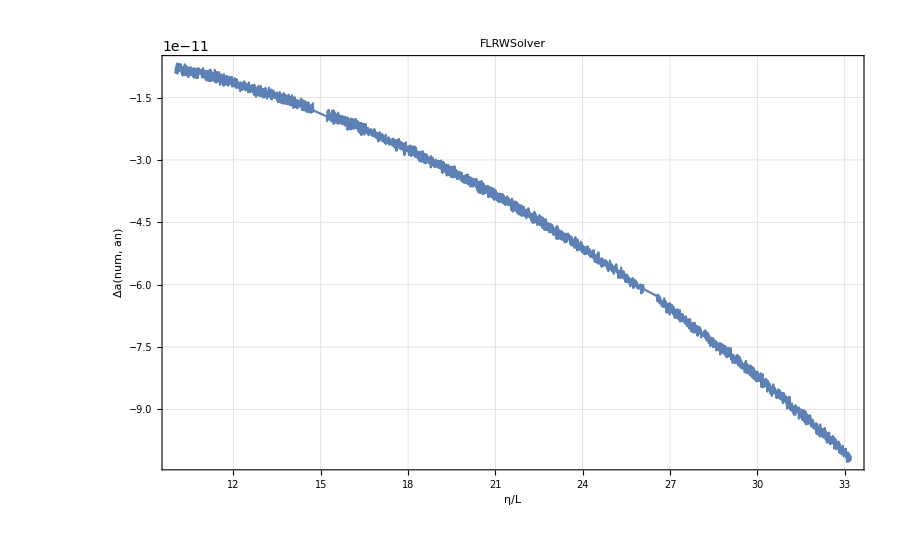

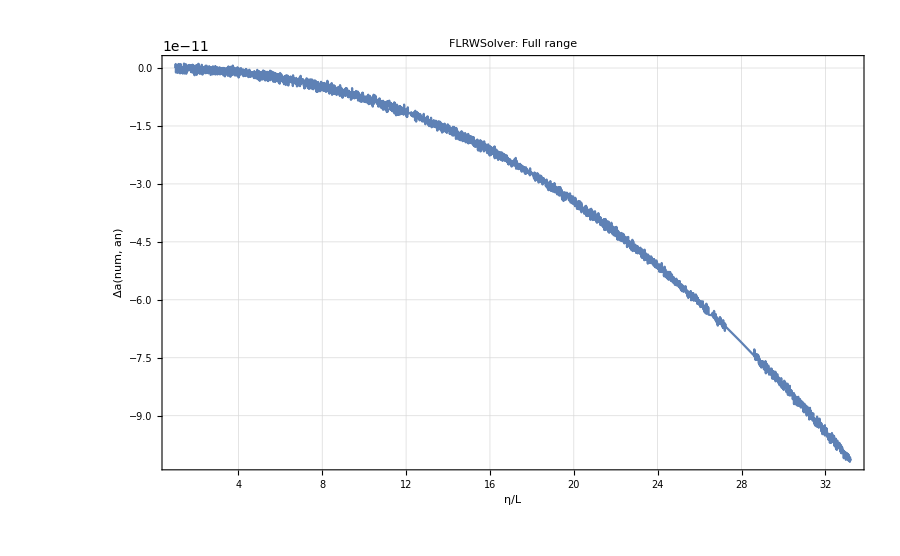

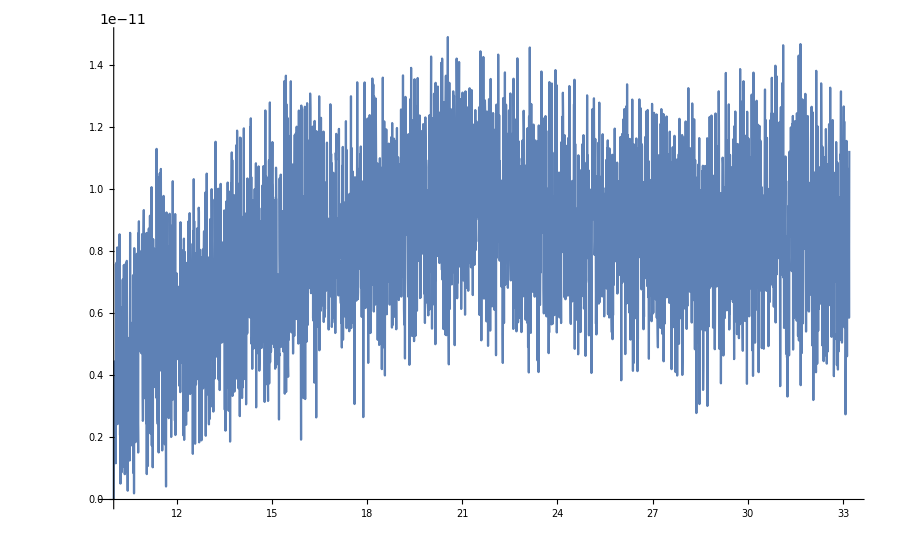

```mathematica
Plot[{(α[η]-A[η])/A[η]},{η,ηin,ETA0},PlotRange->All,WorkingPrecision->30,ImageSize->900,Evaluate[StandardPlotStyle[16,24,"Δa(num, an)","η/L","FLRWSolver",{},{}]]]
Plot[{(α[η]-A[η])/A[η]},{η,iα[[1,1]],iα[[Length@iα,1]]},PlotRange->All,WorkingPrecision->30,ImageSize->900,Evaluate[StandardPlotStyle[16,24,"Δa(num, an)","η/L","FLRWSolver: Full range",{},{}]]]

(*LogLogPlot[Abs[α[η]-η^2],{η,ηin,ETA0},PlotRange->All]
LogLogPlot[Abs[(α[η]-η^2)/η^2],{η,ηin,ETA0},PlotRange->All]
(*Plot[{α[η]-η^2},{η,ηin,ETA0}]*)
Plot[{(α'[η]/α[η]-2/η)/(2/η)},{η,ηin,ETA0}]*)
Plot[(α[η]^3 ρ[η])/(α[ηin]^3 ρ[ηin])-1,{η,ηin,ETA0},PlotRange->All,WorkingPrecision->30]
```

```mathematica
γ={{γxx[η],γxy[η],γxz[η]},{γxy[η],γyy[η],γyz[η]},{γxz[η],γyz[η],γzz[η]}};
```

```mathematica
𝒦={{kxx[η],kxy[η],kxz[η]},{kxy[η],kyy[η],kyz[η]},{kxz[η],kyz[η],kzz[η]}};
```

```mathematica
β={0,0,0};
nu=Join[{1/α[η]},-β/α[η]]
nd={-α[η],0,0,0}
(*β[η_]:={0,0,0};
nu[η_]:=Join[{1/α[η]},-β[η]/α[η]]
nd[η_]:={-α[η],0,0,0}*)
```

{1/(InterpolatingFunction[{{1.000000000000000, 33.19950000000000}}, <>][η]),0,0,0}

{-InterpolatingFunction[{{1.000000000000000, 33.19950000000000}}, <>][η],0,0,0}

```mathematica
X4={η,x,y,z};
X={x,y,z};
V={v1,v2,v3};
e={e1,e2,e3};
Energy={energy, λ};
```

## Geodesic

```mathematica
Clear[γxx, γxy,γyy,γxz,γyz,γzz, kxx,kxy,kyy,kxz,kyz,kzz]
```

```mathematica
?GeodesicEquations
?EnergyEquations
```

GeodesicEquations[X^i,V^i,γ_ij, K_ij, α, β, time]. Returns the geodesic equation in 3+1 form. It contains the RHS for dx/dt and dV/dt

EnergyEquations[γ_ij, K_ij, α, β, {E,λ},X^i,V^i, time]. Returns the equations for dλ/dt and dE/dt

```mathematica
geodBG=GeodesicEquations[X,V,γ,𝒦,α[η],β,η];
```

```mathematica
enereqBG=EnergyEquations[γ,𝒦,α[η],β,Energy,X,V,η];
```

```mathematica
γxx=SetPrecision[Interpolation[iγxx],prec];
γxy=SetPrecision[Interpolation[iγxy],prec];
γxz=SetPrecision[Interpolation[iγxz],prec];
γyy=SetPrecision[Interpolation[iγyy],prec];
γyz=SetPrecision[Interpolation[iγyz],prec];
γzz=SetPrecision[Interpolation[iγzz],prec];
kxx=SetPrecision[Interpolation[ikxx],prec];
kxy=SetPrecision[Interpolation[ikxy],prec];
kxz=SetPrecision[Interpolation[ikxz],prec];
kyy=SetPrecision[Interpolation[ikyy],prec];
kyz=SetPrecision[Interpolation[ikyz],prec];
kzz=SetPrecision[Interpolation[ikzz],prec];
```

```mathematica
αα[τ_]:=α[τ]
ββ[τ_]:=β/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
VV[η_]:=Table[V[[i]][η],{i,1,Length[X]}];
gg[τ_]:=γ/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
(*gg4[τ_]:=g4/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];*)
nup[τ_]:=nu/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
ndown[τ_]:=nd/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
(*αα[τ_]:=α/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
ββ[τ_]:=β/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
VV[η_]:=Table[V[[i]][η],{i,1,Length[X]}];
gg[τ_]:=g/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
gg4[τ_]:=g4/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
nup[τ_]:=nu/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
ndown[τ_]:=nd/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];*)
αlup[η_]:=(*EBG[η]*)αα[η] (nup[η]+Flatten[{0,VV[η]}]);
αldown[η_]:=(*EBG[η]*)αα[η](ndown[η]+Flatten[{0,gg[η].VV[η]}]);
g4[η_]:={{-(α[η])^2+ββ[η].ββ[η],ββ[η][[1]],ββ[η][[2]],ββ[η][[3]]},{ββ[η][[1]],γxx[η],γxy[η],γxz[η]},{ββ[η][[2]],γxy[η],γyy[η],γyz[η]},{ββ[η][[3]],γxz[η],γyz[η],γzz[η]}};
K4[η_]:={{0,0,0,0},{0,kxx[η],kxy[η],kxz[η]},{0,kxy[η],kyy[η],kyz[η]},{0,kxz[η],kyz[η],kzz[η]}};
```

### Initial conditions

The initial conditions can be given in two different ways:
1) directly specifying the values or
2) giving the initial direction v^2 and v^3 and use the function InitialConditions[] to compute v^1 such that the geodesic is null.
Here we set the initial tangent vector as  ℓ^μ=(𝓋^0(∂_0))^μ+Γ (N⃗)^μ which is null with the choice 𝓋^0==-1 and Γ ==1 for any direction (N⃗)^μand we perform the 3+1 splitting with Vsplit[].
 Then we check that is actually null by using the InitialConditions[] function

```mathematica
κ=SetPrecision[𝒱[-1,1,π/4,π/4],prec]
```

{-1.,0.5,0.5,0.7071067811865475}

```mathematica
(g4[η].κ.κ)/.η->ηin
```

2.54×10^-8

```mathematica
?Vsplit
```

Vsplit[𝒱^μ,n^μ,n_μ]. Returns the 3+1 form of a four-vector as 𝒱=vecN( n^μ + vecT^μ) given the normal vector n^μ and n_μ]

The vector κ^μ must be expressed in 3+1 form κ^μ=E(n^μ+V^μ) where E=-κ^μ n_μ and V^μ=κ^μ/E-n^μ

```mathematica
ℓsplit=Vsplit[κ,nup[ηin],ndown[ηin]];
```

3+1 Initial conditions

```mathematica
substitution={η->ηin,x->0,y->0,z->0,v2->ℓsplit[[2,2]],v3->ℓsplit[[2,3]]};
```

```mathematica
?InitialConditions
```

InitialConditions[γ_ij, {(V^2)_in,(V^3)_in, (X^i)_in}, V^i, param]. Compute the initial value for the first spatial component V^1 using the spatial null condition γ_ijV^iV^j==1

```mathematica
initialvel1=Flatten[InitialConditions[γ,substitution,V,param]]
initialBG=Flatten[Join[Table[(substitution[[i,1]][η]/.substitution[[1]])==substitution[[i,2]],{i,2,Length[substitution]}],{(V[[1]][η]/.substitution[[1]])==initialvel1[[2,2]]}]]
E0BG=ℓsplit[[1]]
initialenergy={Energy[[1]][ηin]==E0BG,Energy[[2]][ηin]==1}
```

{v1→-0.0049895165143987,v1→0.0049895165143987}

{x[10.0105]==0,y[10.0105]==0,z[10.0105]==0,v2[10.0105]==-0.00498951651442401,v3[10.0105]==-0.00705624192438296,v1[10.0105]==0.0049895165143987}

-100.210110249073

{energy[10.0105]==-100.210110249073,λ[10.0105]==1}

The four-velocity of the observer  in 3+1 decomposition is u^μ=Γ(n^μ+U^μ): in this case the homogeneity impose that every observer and source move together with the cosmic expansion. This implies that the observer is static with respect to the cosmic flow (no spatial velocity U^i=0) and that the Lorentz factor is Γ=1 (which follows from the normalization u^μ u_μ=-1)

```mathematica
U={0,0,0};
Γl=Sqrt[1/(1-γ.U.U)]
uu=Γl(nup[η]+Join[{0},U])

u[τ_]:=uu/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
u[ETA0]//N
u[ηin]//N
```

1

{1/(InterpolatingFunction[{{1.000000000000000, 33.19950000000000}}, <>][η]),0,0,0}

{0.000907271,0.,0.,0.}

{0.00997903,0.,0.,0.}

### Solve the equations numerically, given the functions in the metric explicitly

```mathematica
?SolveGeodesic
?SolveEnergy
```

SolveGeodesic[geod_eq, initial_conditions, X^i,V^i,param, time, tin,tfin, method, workingprecision_,precision_,interpolation_, number_maxsteps]. Solve the ODE for the geodesic equations and returns the position and the tangent vectors

SolveEnergy[energy_eq, initial_conditions, {E,λ}, geodesic_solution, param, time, tin,tfin, method, workingprecision_,precision_,interpolation_, number_maxsteps]. Solve the ODE for the energy

```mathematica
AbsoluteTiming[With[{opts=SystemOptions[]},Internal`WithLocalSettings[SetSystemOptions["NDSolveOptions"->"DefaultSolveTimeConstraint"->40.],solgeodesic=Flatten[SolveGeodesic[geodBG,initialBG,X,V,param,η,ηin,ETA0,"SS",40,prec,10,15]];,SetSystemOptions[opts]]]]
```

NDSolve::precw: The precision of the differential equation ({{«1»},{},{},{},{}}) is less than WorkingPrecision (40.).

SystemOptions::noset: The value of SystemOption PreemptiveCheckUseThreads cannot be modified.

{155.231,Null}

```mathematica
AbsoluteTiming[With[{opts=SystemOptions[]},Internal`WithLocalSettings[SetSystemOptions["NDSolveOptions"->"DefaultSolveTimeConstraint"->40.],solenergy=Flatten[SolveEnergy[enereqBG,initialenergy,Energy,solgeodesic,param,η,ηin,ETA0,"SS",40,prec,10,15]];,SetSystemOptions[opts]]]]
```

NDSolve::precw: The precision of the differential equation ({{energy'[η]==energy[η] «1»[η] (InterpolatingFunction[{«1»},{«13»},{«1»},{«64400»},{«1»}][η] (InterpolatingFunction[«5»][«1»])^2+«4»+InterpolatingFunction[{«1»},{«13»},{«1»},{«64400»},{«1»}][η] (InterpolatingFunction[«5»][«1»])^2),λ'[η]==(«1»[η])/energy[η],energy[«45»]==-«58»,λ[10.0105]==1},{},{},{},{}}) is less than WorkingPrecision (40.).

SystemOptions::noset: The value of SystemOption PreemptiveCheckUseThreads cannot be modified.

{70.3984,Null}

Test that the constraint conditions are satisfied for all the evolution

```mathematica
geodesic=Join[solgeodesic,solenergy];
```

```mathematica
Join[solgeodesic,solenergy]>>"FLRWSolver_StoO_geodesic_bisect_0p05.m";
```

```mathematica
geodesic=<<"FLRWSolver_StoO_geodesic_bisect_0p05.m";
```

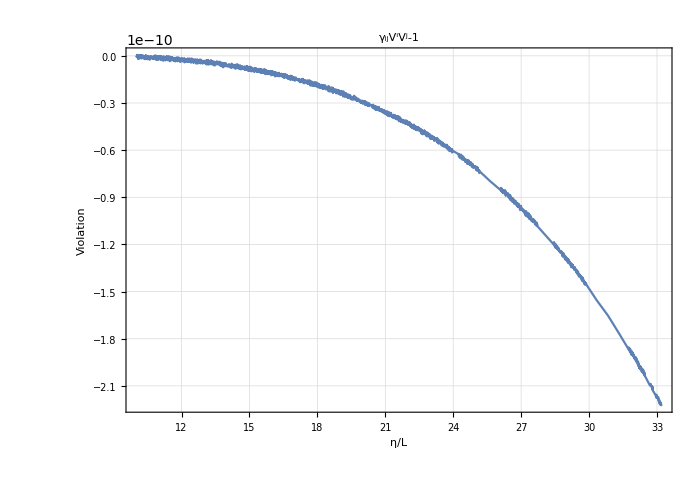

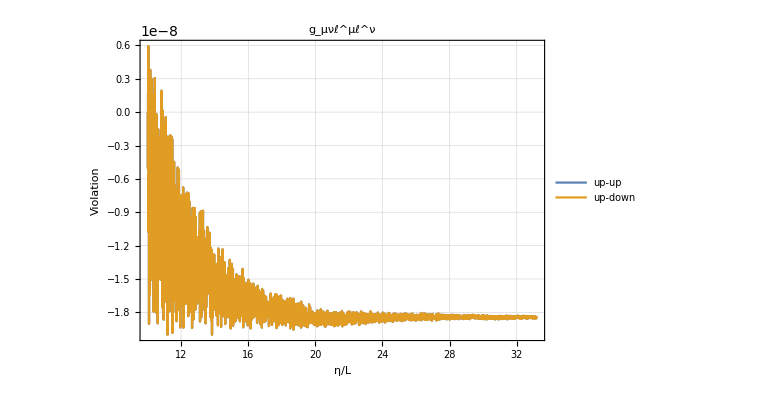

```mathematica
EBG[η_]:=energy[η]/.geodesic;
lup[η_]:=EBG[η](nup[η]+Flatten[{0,VV[η]}]);
ldown[η_]:=EBG[η](ndown[η]+Flatten[{0,gg[η].VV[η]}]);
titolo=Plot[Evaluate[{gg[η].VV[η].VV[η]-1}/.geodesic/.param], {η, ηin,ETA0},PlotRange->All,WorkingPrecision->60,AspectRatio->0.7,ImageSize->700,Evaluate[StandardPlotStyle[16,24,"Violation","η/L","γ_ijV^iV^j-1",{},{}]]]
Plot[Evaluate[{g4[η].lup[η].lup[η],lup[η].ldown[η]}/.geodesic/.param], {η, ηin,ETA0},PlotRange->Full,WorkingPrecision->60,AspectRatio->0.7,ImageSize->Large,Evaluate[StandardPlotStyle[16,24,"Violation","η/L","g_μνℓ^μℓ^ν",{"up-up","up-down"},{0.6,0.6}]]]
```

### Compute the redshift

The  redshift is defined as z+1==(g_μν u^μ ℓ^ν|_𝒮)/(g_μν u^μ ℓ^ν|_𝒪). 
In 3+1, decomposing u^μ==Γ(n^μ+U^μ) and ℓ^μ=ℰ(n^μ+V^μ), the redshift becomes: z+1==ℰ_𝒮/ℰ_𝒪(1-γ_ij V^i U^j|_𝒮)/(1-γ_ij V^i U^j|_𝒪)((1-γ_ij U^i U^j|_𝒮)/(1-γ_ij U^i U^j|_𝒪))^(1/2). In synchronous-comoving coordinates U^i==0 and the redshift simplifies to z+1==ℰ_𝒮/ℰ_𝒪

```mathematica
redshift[η_]:=EBG[η]/EBG[ETA0]-1(*A[ETA0]/A[η]-1*)
```

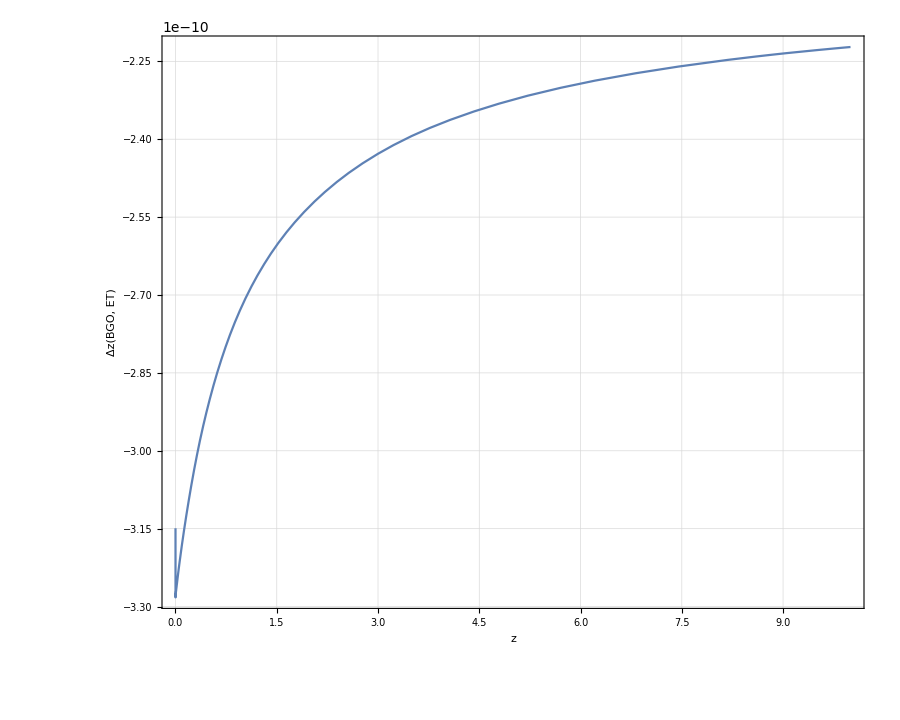

```mathematica
ParametricPlot[{redshift[η], ( redshift[η]/(A[ETA0]/A[η]-1)-1)},{η,ηin,ETA0},(*WorkingPrecision->40,*)ImageSize->900,AspectRatio->0.8,PlotRange->All,Evaluate[StandardPlotStyle[18,24,"Δz(BGO, ET)","z"," ",{},{}]]]
```

#### Comparison analytic geodesic

```mathematica
lup[ETA0]/.geodesic
lup[ηin]/.geodesic
```

{-1.,0.50000000000439,0.5,0.70710678118655}

{-1.2148598302755×10^6,607429.915141826,607429.91513649,859035.624177163}

```mathematica
𝓀an[η_]:={A[ETA0]^2/A[η]^2(-1)(*lup[ETA0][[1]]*),A[ETA0]^2/A[η]^2 lup[ETA0][[2]],A[ETA0]^2/A[η]^2 lup[ETA0][[3]],A[ETA0]^2/A[η]^2 lup[ETA0][[4]]}/.geodesic
```

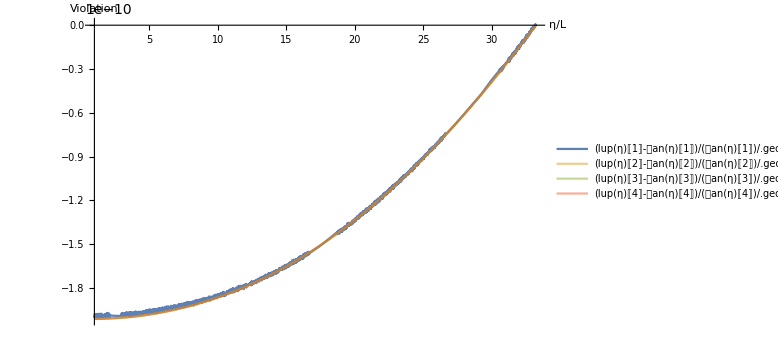

```mathematica
Plot[{((lup[η][[1]]-𝓀an[η][[1]])/(𝓀an[η][[1]]))/.geodesic,((lup[η][[2]]-𝓀an[η][[2]])/(𝓀an[η][[2]]))/.geodesic,((lup[η][[3]]-𝓀an[η][[3]])/(𝓀an[η][[3]]))/.geodesic,((lup[η][[4]]-𝓀an[η][[4]])/(𝓀an[η][[4]]))/.geodesic},{η,ηin,ETA0},PlotRange->All, AxesLabel->{"η/L","Violation"},PlotLegends->"Expressions",PlotStyle->{Thick,Opacity[0.5],Opacity[0.5],Opacity[0.5]},ImageSize->Large]
```

```mathematica
trajectoryBG[η_]:=Flatten[{x[η] ,y[η] ,z[η] }/.geodesic/.param];
𝓍in={x,y,z}/.substitution;
𝓍an[η_]:=Take[κ,-3](η-ηin)+𝓍in
```

```mathematica
𝓍an[ηin]
```

{0.,0.,0.}

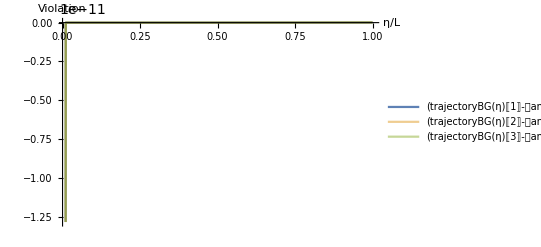

```mathematica
Plot[{(trajectoryBG[η][[1]]-𝓍an[η][[1]])/(𝓍an[η][[1]]),(trajectoryBG[η][[2]]-𝓍an[η][[2]])/(𝓍an[η][[2]]),(trajectoryBG[η][[3]]-𝓍an[η][[3]])/(𝓍an[η][[3]])},{η,ηin,ETA0},PlotRange->All,AxesLabel->{"η/L","Violation"},PlotLegends->"Expressions",PlotStyle->{Thick,Opacity[.5],Opacity[.5]}]
```

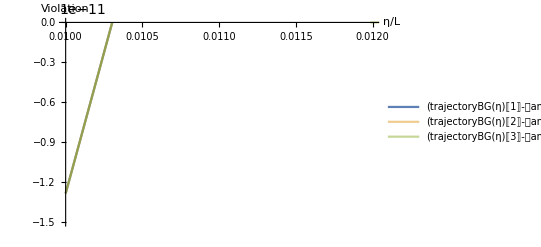

```mathematica
Plot[{(trajectoryBG[η][[1]]-𝓍an[η][[1]])/(𝓍an[η][[1]]),(trajectoryBG[η][[2]]-𝓍an[η][[2]])/(𝓍an[η][[2]]),(trajectoryBG[η][[3]]-𝓍an[η][[3]])/(𝓍an[η][[3]])},{η,ηin,ETA0},PlotRange->{{ηin,0.012},{-1.5 10^-11,0}},AxesLabel->{"η/L","Violation"},PlotLegends->"Expressions",PlotStyle->{Thick,Opacity[.5],Opacity[.5]}]
```

#### Compute the null geodesic

```mathematica
trajectoryBG[η_]:=Flatten[{x[η] ,y[η] ,z[η] }/.geodesic/.param];
Show[ParametricPlot3D[{1/A[η] trajectoryBG[η],trajectoryBG[η]},{η,ηin,ETA0},PlotRange->All, ImageSize->700, ViewPoint->{0,0,Infinity}, AxesLabel->{"X/L","Y/L","Z/L"}]/.Line[x_]:>Sequence[Arrowheads[Table[.02,{100/10}]],Arrow@Line[x]] ]
```

-Graphics3D-

## Parallel transport of a frame

```mathematica
Clear[transport2,vecbcframe,soltrans2,soldeviation,solGDE,tot1,tot2,totl,totu,Cu,Cl,Cf1,Cf2,Pu,Pl,P1,P2,F,F0,EE,EE0,OPT,ξ,ξA,ξbc,Ξ,ξ4,DA,DAbc,DAsolGDE,JMAP,frame,frame0]
```

```mathematica
frame0={fu0,f10,f20,fl0};
frame={{fu1,fu2,fu3},{f11,f12,f13},{f21,f22,f23},{fl1,fl2,fl3}};
```

### set-up the initial conditions for the SNF

Let us start setting the four-velocity of the observer that in 3+1 decomposition is u^μ=Γ(n^μ+U^μ): in this case the homogeneity impose that every observer and source move together with the cosmic expansion. This implies that the observer is static with respect to the cosmic flow (no spatial velocity U^i=0) and that the Lorentz factor is Γ=1 (which follows from the normalization u^μ u_μ=-1)

```mathematica
g4[ηin].u[ηin].lup[ηin]/.Join[geodesic,param]
g4[η].u[η].u[η]/.η->ηin
g4[η].u[η].u[η]/.η->ETA0
-1/A[ηin]^2
```

100.21011024907

-1

-1

-0.0000995811001889971

```mathematica
?SNF
```

SNF[g_μν,u^μ,ℓ^μ,p_1^μ,p_2^μ,n^μ,n_μ]. Returns the initial conditions for the SNF in 3+1 given initial values for: the four dimensional metric g_μν four-velocity u^μ, the tangent vector ℓ^μ, two versors p_1^μ and p_2^μ and the normal n^μ and n_μ. The procedure is to write f_1^μ and f_2^μ, and use the relations of the SNF to determine A, B, C, D and E.

```mathematica
p1={0,0,1,0};
p2={0,0,0,1};
```

```mathematica
snfSplit=SNF[g4[ηin],u[ηin],lup[ηin]/.geodesic,p1,p2,nup[ηin],ndown[ηin]]
```

{{1.,{0,0,0}},{0.,{0.002880698702719,0.0086420961081718,-0.004073923174517}},{0.,{0.008147846349023,0.,0.005761397405431}},{-100.21011024907,{-0.49999999999747,0.5,0.70710678118655}}}

### Parallel transport the SNF

```mathematica
initialframeBG=Table[Flatten[{frame0[[i]][ηin]==snfSplit[[i,1]],Table[frame[[i,j]][ηin]==snfSplit[[i,2]][[j]],{j,1,3}]}],{i,1,4}];
```

```mathematica
?PTransportedFrame
```

PTransportedFrame[γ_ij, K_ij, α, β^i, geod_sol, frame_initialCond, (ϕ^i)_(a), (ϕ^0)_(a), param, time, tin,tfin, method, workingprecision_,precision_,interpolation_, number_maxsteps]. Compute and solve the parallel transport equation for the semi-null frame (ϕ^μ)_(a)={u^μ,(ϕ^μ)_(1),(ϕ^μ)_(2),k^μ} in 3+1 form.

```mathematica
AbsoluteTiming[With[{opts=SystemOptions[]},Internal`WithLocalSettings[SetSystemOptions["NDSolveOptions"->"DefaultSolveTimeConstraint"->40.],soltransBG=Flatten[PTransportedFrame[γ,𝒦,α[η],β,geodesic,initialframeBG,frame,frame0,param,η,ηin,ETA0,"SS",40,prec,10,15]];,SetSystemOptions[opts]]]]
```

NDSolve::precw: The precision of the differential equation ({{fu0'[η]==InterpolatingFunction[{{1.,33.1995}},{5,3,0,{64400},{4},0,0,0,0,Automatic,{},{},False},{{«1»}},{{1.},{1.00100024999915},{1.00200100000062},«46»,{1.04960025000032},«64350»},{Automatic}][η] («1»),«6»,«1»},«3»,{}}) is less than WorkingPrecision (40.).

NDSolve::precw: The precision of the differential equation ({{f10'[η]==InterpolatingFunction[{{1.,33.1995}},{5,3,0,{64400},{4},0,0,0,0,Automatic,{},{},False},{{«1»}},{{1.},{1.00100024999915},{1.00200100000062},«46»,{1.04960025000032},«64350»},{Automatic}][η] («1»),«6»,«1»},«3»,{}}) is less than WorkingPrecision (40.).

NDSolve::precw: The precision of the differential equation ({{f20'[η]==InterpolatingFunction[{{1.,33.1995}},{5,3,0,{64400},{4},0,0,0,0,Automatic,{},{},False},{{«1»}},{{1.},{1.00100024999915},{1.00200100000062},«46»,{1.04960025000032},«64350»},{Automatic}][η] («1»),«6»,«1»},«3»,{}}) is less than WorkingPrecision (40.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

SystemOptions::noset: The value of SystemOption PreemptiveCheckUseThreads cannot be modified.

{2997.12,Null}

```mathematica
totBG=Flatten[Join[Flatten[soltransBG],geodesic]];
```

```mathematica
Cu[η_]:=fu0[η];
Cf1[η_]:=f10[η];
Cf2[η_]:=f20[η];
Cl[η_]:=fl0[η];
Pu[η_]:={fu1[η],fu2[η],fu3[η]};
P1[η_]:={f11[η],f12[η],f13[η]};
P2[η_]:={f21[η],f22[η],f23[η]};
Pl[η_]:={fl1[η],fl2[η],fl3[η]};
```

```mathematica
Show[ParametricPlot3D[trajectoryBG[η],{η,ηin,ETA0},PlotRange->All]/.Line[x_]:>Sequence[Arrowheads[Table[.02,{100/10}]],Arrow@Line[x]] ,Graphics3D[{(*{Red,Arrowheads[0.02],Table[Arrow[{trajectoryBG[η],(trajectoryBG[η]+(Pu[η]/.totBG))}],{η,ηin,ETA0,0.05}]},*){Green,Arrowheads[0.02],Table[Arrow[{trajectoryBG[η],(trajectoryBG[η]+α[η](P1[η]/.totBG))}],{η,ηin,ETA0,1}]},{Blue,Arrowheads[0.02],Table[Arrow[{trajectoryBG[η],(trajectoryBG[η]+α[η](P2[η]/.totBG))}],{η,ηin,ETA0,1}]}(*,{Black,Arrowheads[0.02],Table[Arrow[{trajectoryBG[η],(trajectoryBG[η]+(Pl[η]/.totBG))}],{η,ηin,ETA0,0.05}]}*)}],Graphics3D[Sphere[{0,0,0},0.05]] , ImageSize->700,ViewPoint->{0,100,10},AxesLabel->{x,y,z},AxesStyle->Directive[Red,12]]
```

-Graphics3D-

```mathematica
totBG=<<"FLRWSolver_StoO_ptSNFN_bisect_0p05.m";
```

### Define the induced metric of the SNF “h”

```mathematica
Clear[F,F0,EE,EE0,Q,h]
```

```mathematica
(*Q=Re[((g4[ETA0].(Evaluate[Cu[ETA0]nup[ETA0]+Flatten[{0, Pu[ETA0]}]]).(Evaluate[Cl[ETA0]nup[ETA0]+Flatten[{0, Pl[ETA0]}]]))/.totBG/.param)];*)
Q=ldown[ηin].u[ηin]/.geodesic;
h={{-1,0,0,Q},{0,1,0,0},{0,0,1,0},{Q,0,0,0}};
Ih=Inverse[h];
```

```mathematica
F[t_]:={{Pu[t][[1]],P1[t][[1]],P2[t][[1]],Pl[t][[1]]},{Pu[t][[2]],P1[t][[2]],P2[t][[2]],Pl[t][[2]]},{Pu[t][[3]],P1[t][[3]],P2[t][[3]],Pl[t][[3]]}};
F0[t_]:={Cu[t],Cf1[t],Cf2[t],Cl[t]};
```

```mathematica
totBG>>"FLRWSolver_StoO_ptSNFN_bisect_0p05.m"
```

#### Check SNF

```mathematica
Check of the relations: u^μ Subscript[u, μ]=-1,f1^μ Subscript[f1, μ]=1,f2^μ Subscript[f2, μ]=1,k^μ Subscript[k, μ]=0
```

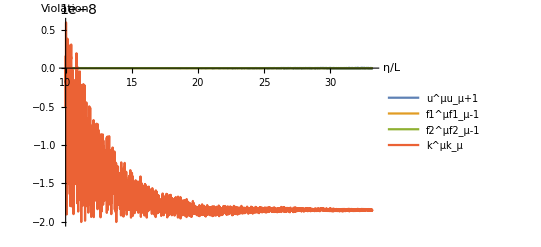

```mathematica
Plot[{(g4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]])+1)/.totBG/.param,(g4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]])-1)/.totBG/.param,(g4[η].(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]])-1)/.totBG/.param,(g4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]))/.totBG/.param},{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"u^μu_μ+1","f1^μf1_μ-1","f2^μf2_μ-1","k^μk_μ"},PlotRange->All(*{-10^-6,10^-6}*),WorkingPrecision->30]
```

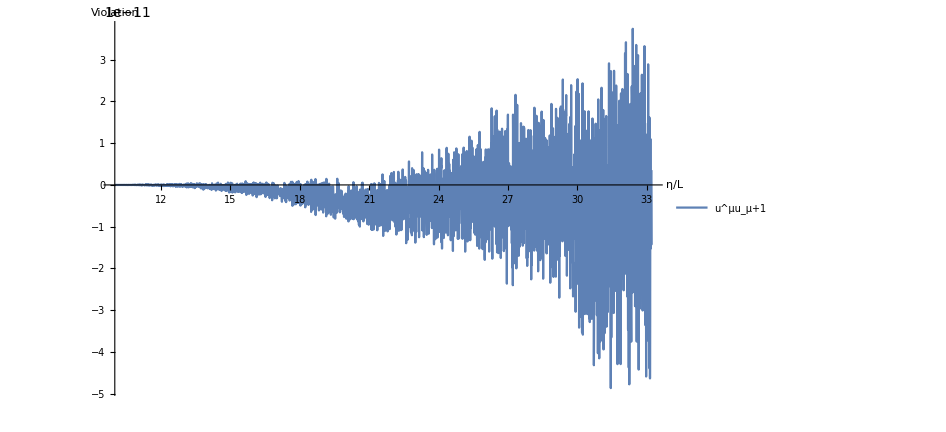

```mathematica
Plot[(g4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]])+1)/.totBG/.param,{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"u^μu_μ+1","f1^μf1_μ-1","f2^μf2_μ-1","k^μk_μ"},PlotRange->Full,WorkingPrecision->30,ImageSize->700]
```

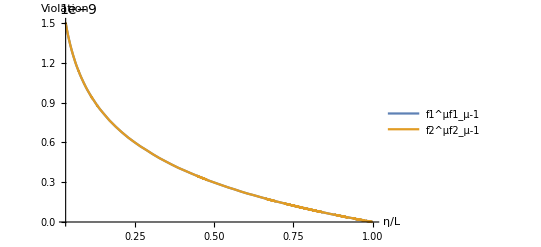

```mathematica
Plot[{(g4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]])-1)/.totBG/.param,(g4[η].(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]])-1)/.totBG/.param},{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"f1^μf1_μ-1","f2^μf2_μ-1"},PlotRange->All(*{-10^-6,10^-6}*),WorkingPrecision->30]
```

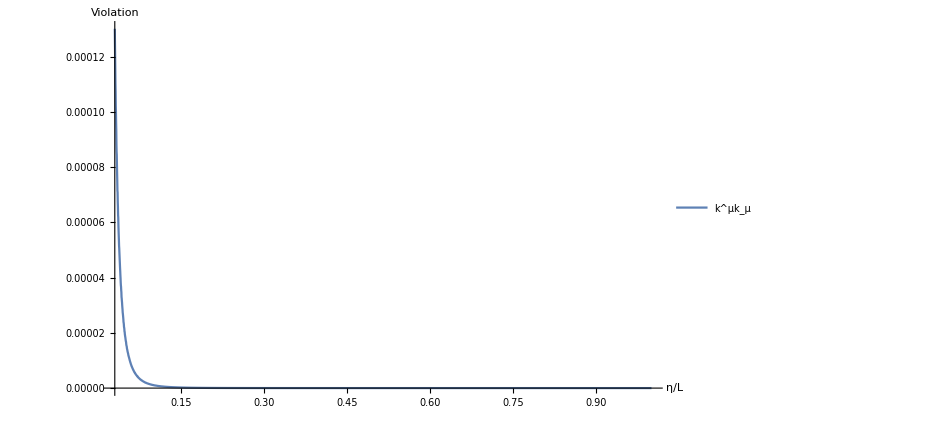

```mathematica
Plot[(g4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]))/.totBG/.param,{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"k^μk_μ"},PlotRange->Full,WorkingPrecision->30,ImageSize->700]
```

```mathematica
Check of the relations: u^μ Subscript[f1, μ]=0,u^μ Subscript[f2, μ]=0,k^μ Subscript[f1, μ]=0,k^μ Subscript[f2, μ]=0
```

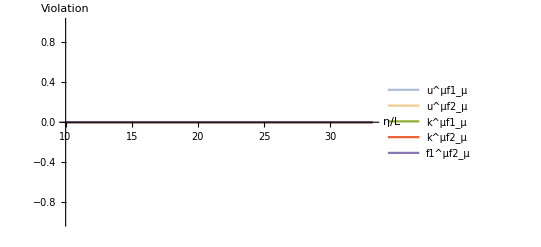

```mathematica
Plot[{(g4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]))/.totBG/.param,(g4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param,(g4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]))/.totBG/.param,(g4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param,(g4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param},{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"u^μf1_μ","u^μf2_μ","k^μf1_μ","k^μf2_μ","f1^μf2_μ"},PlotRange->All(*{{tin,t0},{-10^-8,10^-8}}*),PlotStyle->{Opacity[.5],Opacity[.5],Thick,Thick,Thick},WorkingPrecision->30]
```

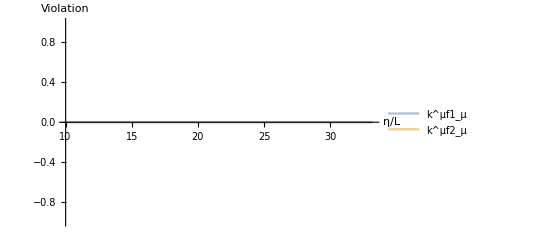

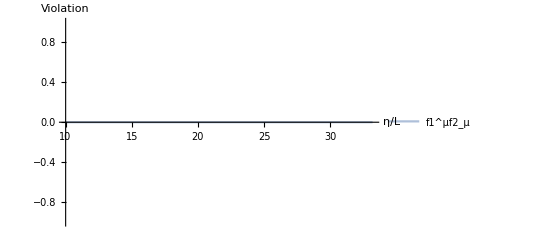

```mathematica
Plot[{(g4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]))/.totBG/.param,(g4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param},{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"k^μf1_μ","k^μf2_μ"},PlotRange->All(*{{tin,t0},{-10^-8,10^-8}}*),PlotStyle->{Opacity[.5],Opacity[.5],Thick,Thick,Thick},WorkingPrecision->30]
Plot[{(g4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param},{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"f1^μf2_μ"},PlotRange->All(*{{tin,t0},{-10^-8,10^-8}}*),PlotStyle->{Opacity[.5],Opacity[.5],Thick,Thick,Thick},WorkingPrecision->30]
```

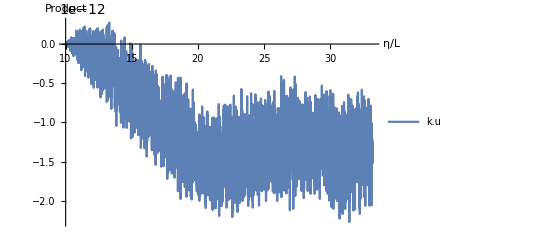

```mathematica
Plot[(((((g4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]])))/((ldown[ηin].u[ηin]))))/.totBG/.param)-1,{η,ηin,ETA0},AxesLabel->{"η/L","Product"},PlotLegends->{"k.u"},PlotRange->All,WorkingPrecision->30]
```

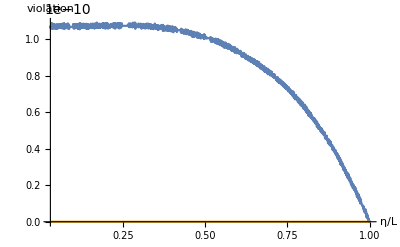

```mathematica
Plot[Evaluate[{(gg[η].VV[η].VV[η]-1),0( gg[η].Pl[η].Pl[η]-Cl[η]^2) (*( (gg[η].Pl[η].Pl[η]-Cl[η]^2)/Cl[η]^2) *)}/.totBG/.param], {η, ηin,ETA0},PlotRange->Full,AxesLabel->{Style["η/L",Large],Style["violation",Large]}]
```

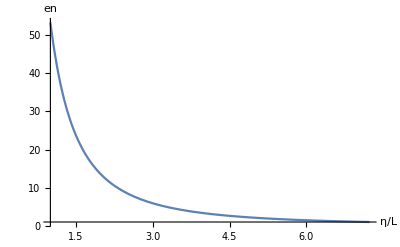

```mathematica
Plot[(A[ηin]^2/A[η]-Cl[η])/.totBG,{η, ηin,ETA0},PlotRange->Full,AxesLabel->{Style["η/L",Large],Style["en",Large]}]
```

## Optical Tidal Matrix

```mathematica
Clear[α,γ,𝒦,γxx,γxy,γxz,γyy,γyz,γzz,kxx,kxy,kxz,kyy,kyz,kzz]
```

```mathematica
γ={{γxx[η],γxy[η],γxz[η]},{γxy[η],γyy[η],γyz[η]},{γxz[η],γyz[η],γzz[η]}};

𝒦={{kxx[η],kxy[η],kxz[η]},{kxy[η],kyy[η],kyz[η]},{kxz[η],kyz[η],kzz[η]}};
```

```mathematica
?OpticalTidalMatrix
```

OpticalTidalMatrix[X^i,V^i, (ϕ^i)_(a), (ϕ^0)_(a), Q, γ_ij, K_ij, α, β^i, time]. Returns the optical tidal matrix computed using only 3+1 quantities. The basic idea is to take the contraction of the full Riemann with the tangent vector and the frame vectors (ϕ^μ)_(a) splitted in 3+1. This will give the different parts of the Riemann 
decomposition along n^μ and γ_ij. Using the Riemann's symmetries and the expression for the non-vanishing projection (known as the Gauss, Codazzi e Ricci relations), we obtain the optical tidal matrix in the frame (R^(a))_(kk (b))

```mathematica
Timing[OPT=OpticalTidalMatrix[X,V,frame,frame0,Q,γ,𝒦,α[η],β,η];]
```

{13.8007,Null}

```mathematica
OPT//MatrixForm
```

(0 | 0 | 0 | 0
f12[η] fu2[η] (kxy[η]^2-kxx[η] kyy[η]) v1[η]^2+f13[η] fu2[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f12[η] fu3[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f13[η] fu3[η] (kxz[η]^2-kxx[η] kzz[η]) v1[η]^2+f12[η] fu1[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+f11[η] fu2[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+f13[η] fu1[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+f11[η] fu3[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+f13[η] fu2[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+f12[η] fu3[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+2 f13[η] fu3[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v1[η] v2[η]+f11[η] fu1[η] (kxy[η]^2-kxx[η] kyy[η]) v2[η]^2+f13[η] fu1[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f11[η] fu3[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f13[η] fu3[η] (kyz[η]^2-kyy[η] kzz[η]) v2[η]^2+f12[η] fu1[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+f11[η] fu2[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+2 f12[η] fu2[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v1[η] v3[η]+f13[η] fu1[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+f11[η] fu3[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+f13[η] fu2[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+f12[η] fu3[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+2 f11[η] fu1[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v2[η] v3[η]+f12[η] fu1[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+f11[η] fu2[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+f13[η] fu1[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+f11[η] fu3[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+f13[η] fu2[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f12[η] fu3[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f11[η] fu1[η] (kxz[η]^2-kxx[η] kzz[η]) v3[η]^2+f12[η] fu1[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f11[η] fu2[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f12[η] fu2[η] (kyz[η]^2-kyy[η] kzz[η]) v3[η]^2+((f11[η]-f10[η] v1[η]) (-fu1[η]+fu0[η] v1[η]) (kxz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxx[η]^2 α[η] γyz[η]^2-2 kxz[η] α[η] (kxy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxx[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxx[η]^2 α[η] γyy[η] γzz[η]+kxy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxx[η] kxy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kxx'[η]-2 γxy[η] γxz[η] γyz[η] kxx'[η]+γxx[η] γyz[η]^2 kxx'[η]+γxy[η]^2 γzz[η] kxx'[η]-γxx[η] γyy[η] γzz[η] kxx'[η])+(f12[η] (-fu1[η]+fu0[η] v1[η])+f10[η] v1[η] (fu2[η]-fu0[η] v2[η])) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(f10[η] (fu1[η]-fu0[η] v1[η]) v2[η]+f11[η] (-fu2[η]+fu0[η] v2[η])) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(f13[η] (-fu1[η]+fu0[η] v1[η])+f10[η] v1[η] (fu3[η]-fu0[η] v3[η])) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(f10[η] (fu1[η]-fu0[η] v1[η]) v3[η]+f11[η] (-fu3[η]+fu0[η] v3[η])) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(f12[η]-f10[η] v2[η]) (-fu2[η]+fu0[η] v2[η]) (kyz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxy[η]^2 α[η] γyz[η]^2-2 kyz[η] α[η] (kyy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxy[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxy[η]^2 α[η] γyy[η] γzz[η]+kyy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxy[η] kyy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kyy'[η]-2 γxy[η] γxz[η] γyz[η] kyy'[η]+γxx[η] γyz[η]^2 kyy'[η]+γxy[η]^2 γzz[η] kyy'[η]-γxx[η] γyy[η] γzz[η] kyy'[η])+(f13[η] (-fu2[η]+fu0[η] v2[η])+f10[η] v2[η] (fu3[η]-fu0[η] v3[η])) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(f10[η] (fu2[η]-fu0[η] v2[η]) v3[η]+f12[η] (-fu3[η]+fu0[η] v3[η])) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(f13[η]-f10[η] v3[η]) (-fu3[η]+fu0[η] v3[η]) (kzz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxz[η]^2 α[η] γyz[η]^2-2 kzz[η] α[η] (kyz[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxz[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxz[η]^2 α[η] γyy[η] γzz[η]+kyz[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxz[η] kyz[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kzz'[η]-2 γxy[η] γxz[η] γyz[η] kzz'[η]+γxx[η] γyz[η]^2 kzz'[η]+γxy[η]^2 γzz[η] kzz'[η]-γxx[η] γyy[η] γzz[η] kzz'[η]))/(α[η] (γxz[η]^2 γyy[η]-2 γxy[η] γxz[η] γyz[η]+γxy[η]^2 γzz[η]+γxx[η] (γyz[η]^2-γyy[η] γzz[η]))) | f12[η]^2 (kxy[η]^2-kxx[η] kyy[η]) v1[η]^2+2 f12[η] f13[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f13[η]^2 (kxz[η]^2-kxx[η] kzz[η]) v1[η]^2+2 f11[η] f12[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+2 f11[η] f13[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+2 f12[η] f13[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+2 f13[η]^2 (kxz[η] kyz[η]-kxy[η] kzz[η]) v1[η] v2[η]+f11[η]^2 (kxy[η]^2-kxx[η] kyy[η]) v2[η]^2+2 f11[η] f13[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f13[η]^2 (kyz[η]^2-kyy[η] kzz[η]) v2[η]^2+2 f11[η] f12[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+2 f12[η]^2 (-kxz[η] kyy[η]+kxy[η] kyz[η]) v1[η] v3[η]+2 f11[η] f13[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+2 f12[η] f13[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+2 f11[η]^2 (kxy[η] kxz[η]-kxx[η] kyz[η]) v2[η] v3[η]+2 f11[η] f12[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+2 f11[η] f13[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+2 f12[η] f13[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f11[η]^2 (kxz[η]^2-kxx[η] kzz[η]) v3[η]^2+2 f11[η] f12[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f12[η]^2 (kyz[η]^2-kyy[η] kzz[η]) v3[η]^2+(-(f11[η]-f10[η] v1[η])^2 (kxz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxx[η]^2 α[η] γyz[η]^2-2 kxz[η] α[η] (kxy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxx[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxx[η]^2 α[η] γyy[η] γzz[η]+kxy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxx[η] kxy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kxx'[η]-2 γxy[η] γxz[η] γyz[η] kxx'[η]+γxx[η] γyz[η]^2 kxx'[η]+γxy[η]^2 γzz[η] kxx'[η]-γxx[η] γyy[η] γzz[η] kxx'[η])+(-f11[η] f12[η]+2 f10[η] f11[η] v2[η]-f10[η]^2 v1[η] v2[η]) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(-f11[η] f12[η]+f10[η] v1[η] (2 f12[η]-f10[η] v2[η])) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(-f11[η] f13[η]+2 f10[η] f11[η] v3[η]-f10[η]^2 v1[η] v3[η]) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(-f11[η] f13[η]+f10[η] v1[η] (2 f13[η]-f10[η] v3[η])) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])-(f12[η]-f10[η] v2[η])^2 (kyz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxy[η]^2 α[η] γyz[η]^2-2 kyz[η] α[η] (kyy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxy[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxy[η]^2 α[η] γyy[η] γzz[η]+kyy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxy[η] kyy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kyy'[η]-2 γxy[η] γxz[η] γyz[η] kyy'[η]+γxx[η] γyz[η]^2 kyy'[η]+γxy[η]^2 γzz[η] kyy'[η]-γxx[η] γyy[η] γzz[η] kyy'[η])+(-f12[η] f13[η]+2 f10[η] f12[η] v3[η]-f10[η]^2 v2[η] v3[η]) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(-f12[η] f13[η]+f10[η] v2[η] (2 f13[η]-f10[η] v3[η])) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])-(f13[η]-f10[η] v3[η])^2 (kzz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxz[η]^2 α[η] γyz[η]^2-2 kzz[η] α[η] (kyz[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxz[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxz[η]^2 α[η] γyy[η] γzz[η]+kyz[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxz[η] kyz[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kzz'[η]-2 γxy[η] γxz[η] γyz[η] kzz'[η]+γxx[η] γyz[η]^2 kzz'[η]+γxy[η]^2 γzz[η] kzz'[η]-γxx[η] γyy[η] γzz[η] kzz'[η]))/(α[η] (γxz[η]^2 γyy[η]-2 γxy[η] γxz[η] γyz[η]+γxy[η]^2 γzz[η]+γxx[η] (γyz[η]^2-γyy[η] γzz[η]))) | f12[η] f22[η] (kxy[η]^2-kxx[η] kyy[η]) v1[η]^2+f13[η] f22[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f12[η] f23[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f13[η] f23[η] (kxz[η]^2-kxx[η] kzz[η]) v1[η]^2+f12[η] f21[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+f11[η] f22[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+f13[η] f21[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+f11[η] f23[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+f13[η] f22[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+f12[η] f23[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+2 f13[η] f23[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v1[η] v2[η]+f11[η] f21[η] (kxy[η]^2-kxx[η] kyy[η]) v2[η]^2+f13[η] f21[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f11[η] f23[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f13[η] f23[η] (kyz[η]^2-kyy[η] kzz[η]) v2[η]^2+f12[η] f21[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+f11[η] f22[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+2 f12[η] f22[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v1[η] v3[η]+f13[η] f21[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+f11[η] f23[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+f13[η] f22[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+f12[η] f23[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+2 f11[η] f21[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v2[η] v3[η]+f12[η] f21[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+f11[η] f22[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+f13[η] f21[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+f11[η] f23[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+f13[η] f22[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f12[η] f23[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f11[η] f21[η] (kxz[η]^2-kxx[η] kzz[η]) v3[η]^2+f12[η] f21[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f11[η] f22[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f12[η] f22[η] (kyz[η]^2-kyy[η] kzz[η]) v3[η]^2+((f11[η]-f10[η] v1[η]) (-f21[η]+f20[η] v1[η]) (kxz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxx[η]^2 α[η] γyz[η]^2-2 kxz[η] α[η] (kxy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxx[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxx[η]^2 α[η] γyy[η] γzz[η]+kxy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxx[η] kxy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kxx'[η]-2 γxy[η] γxz[η] γyz[η] kxx'[η]+γxx[η] γyz[η]^2 kxx'[η]+γxy[η]^2 γzz[η] kxx'[η]-γxx[η] γyy[η] γzz[η] kxx'[η])+(-f12[η] f21[η]+f11[η] f20[η] v2[η]+f10[η] (f21[η]-f20[η] v1[η]) v2[η]) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(-f11[η] f22[η]+f12[η] f20[η] v1[η]+f10[η] v1[η] (f22[η]-f20[η] v2[η])) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(-f13[η] f21[η]+f11[η] f20[η] v3[η]+f10[η] (f21[η]-f20[η] v1[η]) v3[η]) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(-f11[η] f23[η]+f13[η] f20[η] v1[η]+f10[η] v1[η] (f23[η]-f20[η] v3[η])) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(f12[η]-f10[η] v2[η]) (-f22[η]+f20[η] v2[η]) (kyz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxy[η]^2 α[η] γyz[η]^2-2 kyz[η] α[η] (kyy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxy[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxy[η]^2 α[η] γyy[η] γzz[η]+kyy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxy[η] kyy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kyy'[η]-2 γxy[η] γxz[η] γyz[η] kyy'[η]+γxx[η] γyz[η]^2 kyy'[η]+γxy[η]^2 γzz[η] kyy'[η]-γxx[η] γyy[η] γzz[η] kyy'[η])+(-f13[η] f22[η]+f12[η] f20[η] v3[η]+f10[η] (f22[η]-f20[η] v2[η]) v3[η]) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(-f12[η] f23[η]+f13[η] f20[η] v2[η]+f10[η] v2[η] (f23[η]-f20[η] v3[η])) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(f13[η]-f10[η] v3[η]) (-f23[η]+f20[η] v3[η]) (kzz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxz[η]^2 α[η] γyz[η]^2-2 kzz[η] α[η] (kyz[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxz[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxz[η]^2 α[η] γyy[η] γzz[η]+kyz[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxz[η] kyz[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kzz'[η]-2 γxy[η] γxz[η] γyz[η] kzz'[η]+γxx[η] γyz[η]^2 kzz'[η]+γxy[η]^2 γzz[η] kzz'[η]-γxx[η] γyy[η] γzz[η] kzz'[η]))/(α[η] (γxz[η]^2 γyy[η]-2 γxy[η] γxz[η] γyz[η]+γxy[η]^2 γzz[η]+γxx[η] (γyz[η]^2-γyy[η] γzz[η]))) | 0
f22[η] fu2[η] (kxy[η]^2-kxx[η] kyy[η]) v1[η]^2+f23[η] fu2[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f22[η] fu3[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f23[η] fu3[η] (kxz[η]^2-kxx[η] kzz[η]) v1[η]^2+f22[η] fu1[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+f21[η] fu2[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+f23[η] fu1[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+f21[η] fu3[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+f23[η] fu2[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+f22[η] fu3[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+2 f23[η] fu3[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v1[η] v2[η]+f21[η] fu1[η] (kxy[η]^2-kxx[η] kyy[η]) v2[η]^2+f23[η] fu1[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f21[η] fu3[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f23[η] fu3[η] (kyz[η]^2-kyy[η] kzz[η]) v2[η]^2+f22[η] fu1[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+f21[η] fu2[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+2 f22[η] fu2[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v1[η] v3[η]+f23[η] fu1[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+f21[η] fu3[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+f23[η] fu2[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+f22[η] fu3[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+2 f21[η] fu1[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v2[η] v3[η]+f22[η] fu1[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+f21[η] fu2[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+f23[η] fu1[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+f21[η] fu3[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+f23[η] fu2[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f22[η] fu3[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f21[η] fu1[η] (kxz[η]^2-kxx[η] kzz[η]) v3[η]^2+f22[η] fu1[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f21[η] fu2[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f22[η] fu2[η] (kyz[η]^2-kyy[η] kzz[η]) v3[η]^2+((f21[η]-f20[η] v1[η]) (-fu1[η]+fu0[η] v1[η]) (kxz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxx[η]^2 α[η] γyz[η]^2-2 kxz[η] α[η] (kxy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxx[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxx[η]^2 α[η] γyy[η] γzz[η]+kxy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxx[η] kxy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kxx'[η]-2 γxy[η] γxz[η] γyz[η] kxx'[η]+γxx[η] γyz[η]^2 kxx'[η]+γxy[η]^2 γzz[η] kxx'[η]-γxx[η] γyy[η] γzz[η] kxx'[η])+(f22[η] (-fu1[η]+fu0[η] v1[η])+f20[η] v1[η] (fu2[η]-fu0[η] v2[η])) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(f20[η] (fu1[η]-fu0[η] v1[η]) v2[η]+f21[η] (-fu2[η]+fu0[η] v2[η])) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(f23[η] (-fu1[η]+fu0[η] v1[η])+f20[η] v1[η] (fu3[η]-fu0[η] v3[η])) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(f20[η] (fu1[η]-fu0[η] v1[η]) v3[η]+f21[η] (-fu3[η]+fu0[η] v3[η])) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(f22[η]-f20[η] v2[η]) (-fu2[η]+fu0[η] v2[η]) (kyz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxy[η]^2 α[η] γyz[η]^2-2 kyz[η] α[η] (kyy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxy[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxy[η]^2 α[η] γyy[η] γzz[η]+kyy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxy[η] kyy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kyy'[η]-2 γxy[η] γxz[η] γyz[η] kyy'[η]+γxx[η] γyz[η]^2 kyy'[η]+γxy[η]^2 γzz[η] kyy'[η]-γxx[η] γyy[η] γzz[η] kyy'[η])+(f23[η] (-fu2[η]+fu0[η] v2[η])+f20[η] v2[η] (fu3[η]-fu0[η] v3[η])) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(f20[η] (fu2[η]-fu0[η] v2[η]) v3[η]+f22[η] (-fu3[η]+fu0[η] v3[η])) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(f23[η]-f20[η] v3[η]) (-fu3[η]+fu0[η] v3[η]) (kzz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxz[η]^2 α[η] γyz[η]^2-2 kzz[η] α[η] (kyz[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxz[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxz[η]^2 α[η] γyy[η] γzz[η]+kyz[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxz[η] kyz[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kzz'[η]-2 γxy[η] γxz[η] γyz[η] kzz'[η]+γxx[η] γyz[η]^2 kzz'[η]+γxy[η]^2 γzz[η] kzz'[η]-γxx[η] γyy[η] γzz[η] kzz'[η]))/(α[η] (γxz[η]^2 γyy[η]-2 γxy[η] γxz[η] γyz[η]+γxy[η]^2 γzz[η]+γxx[η] (γyz[η]^2-γyy[η] γzz[η]))) | f12[η] f22[η] (kxy[η]^2-kxx[η] kyy[η]) v1[η]^2+f13[η] f22[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f12[η] f23[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f13[η] f23[η] (kxz[η]^2-kxx[η] kzz[η]) v1[η]^2+f12[η] f21[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+f11[η] f22[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+f13[η] f21[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+f11[η] f23[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+f13[η] f22[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+f12[η] f23[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+2 f13[η] f23[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v1[η] v2[η]+f11[η] f21[η] (kxy[η]^2-kxx[η] kyy[η]) v2[η]^2+f13[η] f21[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f11[η] f23[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f13[η] f23[η] (kyz[η]^2-kyy[η] kzz[η]) v2[η]^2+f12[η] f21[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+f11[η] f22[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+2 f12[η] f22[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v1[η] v3[η]+f13[η] f21[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+f11[η] f23[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+f13[η] f22[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+f12[η] f23[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+2 f11[η] f21[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v2[η] v3[η]+f12[η] f21[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+f11[η] f22[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+f13[η] f21[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+f11[η] f23[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+f13[η] f22[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f12[η] f23[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f11[η] f21[η] (kxz[η]^2-kxx[η] kzz[η]) v3[η]^2+f12[η] f21[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f11[η] f22[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f12[η] f22[η] (kyz[η]^2-kyy[η] kzz[η]) v3[η]^2+((f11[η]-f10[η] v1[η]) (-f21[η]+f20[η] v1[η]) (kxz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxx[η]^2 α[η] γyz[η]^2-2 kxz[η] α[η] (kxy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxx[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxx[η]^2 α[η] γyy[η] γzz[η]+kxy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxx[η] kxy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kxx'[η]-2 γxy[η] γxz[η] γyz[η] kxx'[η]+γxx[η] γyz[η]^2 kxx'[η]+γxy[η]^2 γzz[η] kxx'[η]-γxx[η] γyy[η] γzz[η] kxx'[η])+(-f12[η] f21[η]+f11[η] f20[η] v2[η]+f10[η] (f21[η]-f20[η] v1[η]) v2[η]) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(-f11[η] f22[η]+f12[η] f20[η] v1[η]+f10[η] v1[η] (f22[η]-f20[η] v2[η])) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(-f13[η] f21[η]+f11[η] f20[η] v3[η]+f10[η] (f21[η]-f20[η] v1[η]) v3[η]) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(-f11[η] f23[η]+f13[η] f20[η] v1[η]+f10[η] v1[η] (f23[η]-f20[η] v3[η])) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(f12[η]-f10[η] v2[η]) (-f22[η]+f20[η] v2[η]) (kyz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxy[η]^2 α[η] γyz[η]^2-2 kyz[η] α[η] (kyy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxy[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxy[η]^2 α[η] γyy[η] γzz[η]+kyy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxy[η] kyy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kyy'[η]-2 γxy[η] γxz[η] γyz[η] kyy'[η]+γxx[η] γyz[η]^2 kyy'[η]+γxy[η]^2 γzz[η] kyy'[η]-γxx[η] γyy[η] γzz[η] kyy'[η])+(-f13[η] f22[η]+f12[η] f20[η] v3[η]+f10[η] (f22[η]-f20[η] v2[η]) v3[η]) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(-f12[η] f23[η]+f13[η] f20[η] v2[η]+f10[η] v2[η] (f23[η]-f20[η] v3[η])) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(f13[η]-f10[η] v3[η]) (-f23[η]+f20[η] v3[η]) (kzz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxz[η]^2 α[η] γyz[η]^2-2 kzz[η] α[η] (kyz[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxz[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxz[η]^2 α[η] γyy[η] γzz[η]+kyz[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxz[η] kyz[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kzz'[η]-2 γxy[η] γxz[η] γyz[η] kzz'[η]+γxx[η] γyz[η]^2 kzz'[η]+γxy[η]^2 γzz[η] kzz'[η]-γxx[η] γyy[η] γzz[η] kzz'[η]))/(α[η] (γxz[η]^2 γyy[η]-2 γxy[η] γxz[η] γyz[η]+γxy[η]^2 γzz[η]+γxx[η] (γyz[η]^2-γyy[η] γzz[η]))) | f22[η]^2 (kxy[η]^2-kxx[η] kyy[η]) v1[η]^2+2 f22[η] f23[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f23[η]^2 (kxz[η]^2-kxx[η] kzz[η]) v1[η]^2+2 f21[η] f22[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+2 f21[η] f23[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+2 f22[η] f23[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+2 f23[η]^2 (kxz[η] kyz[η]-kxy[η] kzz[η]) v1[η] v2[η]+f21[η]^2 (kxy[η]^2-kxx[η] kyy[η]) v2[η]^2+2 f21[η] f23[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f23[η]^2 (kyz[η]^2-kyy[η] kzz[η]) v2[η]^2+2 f21[η] f22[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+2 f22[η]^2 (-kxz[η] kyy[η]+kxy[η] kyz[η]) v1[η] v3[η]+2 f21[η] f23[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+2 f22[η] f23[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+2 f21[η]^2 (kxy[η] kxz[η]-kxx[η] kyz[η]) v2[η] v3[η]+2 f21[η] f22[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+2 f21[η] f23[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+2 f22[η] f23[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f21[η]^2 (kxz[η]^2-kxx[η] kzz[η]) v3[η]^2+2 f21[η] f22[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f22[η]^2 (kyz[η]^2-kyy[η] kzz[η]) v3[η]^2+(-(f21[η]-f20[η] v1[η])^2 (kxz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxx[η]^2 α[η] γyz[η]^2-2 kxz[η] α[η] (kxy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxx[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxx[η]^2 α[η] γyy[η] γzz[η]+kxy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxx[η] kxy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kxx'[η]-2 γxy[η] γxz[η] γyz[η] kxx'[η]+γxx[η] γyz[η]^2 kxx'[η]+γxy[η]^2 γzz[η] kxx'[η]-γxx[η] γyy[η] γzz[η] kxx'[η])+(-f21[η] f22[η]+2 f20[η] f21[η] v2[η]-f20[η]^2 v1[η] v2[η]) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(-f21[η] f22[η]+f20[η] v1[η] (2 f22[η]-f20[η] v2[η])) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(-f21[η] f23[η]+2 f20[η] f21[η] v3[η]-f20[η]^2 v1[η] v3[η]) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(-f21[η] f23[η]+f20[η] v1[η] (2 f23[η]-f20[η] v3[η])) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])-(f22[η]-f20[η] v2[η])^2 (kyz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxy[η]^2 α[η] γyz[η]^2-2 kyz[η] α[η] (kyy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxy[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxy[η]^2 α[η] γyy[η] γzz[η]+kyy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxy[η] kyy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kyy'[η]-2 γxy[η] γxz[η] γyz[η] kyy'[η]+γxx[η] γyz[η]^2 kyy'[η]+γxy[η]^2 γzz[η] kyy'[η]-γxx[η] γyy[η] γzz[η] kyy'[η])+(-f22[η] f23[η]+2 f20[η] f22[η] v3[η]-f20[η]^2 v2[η] v3[η]) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(-f22[η] f23[η]+f20[η] v2[η] (2 f23[η]-f20[η] v3[η])) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])-(f23[η]-f20[η] v3[η])^2 (kzz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxz[η]^2 α[η] γyz[η]^2-2 kzz[η] α[η] (kyz[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxz[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxz[η]^2 α[η] γyy[η] γzz[η]+kyz[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxz[η] kyz[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kzz'[η]-2 γxy[η] γxz[η] γyz[η] kzz'[η]+γxx[η] γyz[η]^2 kzz'[η]+γxy[η]^2 γzz[η] kzz'[η]-γxx[η] γyy[η] γzz[η] kzz'[η]))/(α[η] (γxz[η]^2 γyy[η]-2 γxy[η] γxz[η] γyz[η]+γxy[η]^2 γzz[η]+γxx[η] (γyz[η]^2-γyy[η] γzz[η]))) | 0
1. (fu2[η]^2 (kxy[η]^2-kxx[η] kyy[η]) v1[η]^2+2 fu2[η] fu3[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+fu3[η]^2 (kxz[η]^2-kxx[η] kzz[η]) v1[η]^2+2 fu1[η] fu2[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+2 fu1[η] fu3[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+2 fu2[η] fu3[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+2 fu3[η]^2 (kxz[η] kyz[η]-kxy[η] kzz[η]) v1[η] v2[η]+fu1[η]^2 (kxy[η]^2-kxx[η] kyy[η]) v2[η]^2+2 fu1[η] fu3[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+fu3[η]^2 (kyz[η]^2-kyy[η] kzz[η]) v2[η]^2+2 fu1[η] fu2[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+2 fu2[η]^2 (-kxz[η] kyy[η]+kxy[η] kyz[η]) v1[η] v3[η]+2 fu1[η] fu3[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+2 fu2[η] fu3[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+2 fu1[η]^2 (kxy[η] kxz[η]-kxx[η] kyz[η]) v2[η] v3[η]+2 fu1[η] fu2[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+2 fu1[η] fu3[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+2 fu2[η] fu3[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+fu1[η]^2 (kxz[η]^2-kxx[η] kzz[η]) v3[η]^2+2 fu1[η] fu2[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+fu2[η]^2 (kyz[η]^2-kyy[η] kzz[η]) v3[η]^2+(-(fu1[η]-fu0[η] v1[η])^2 (kxz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxx[η]^2 α[η] γyz[η]^2-2 kxz[η] α[η] (kxy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxx[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxx[η]^2 α[η] γyy[η] γzz[η]+kxy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxx[η] kxy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kxx'[η]-2 γxy[η] γxz[η] γyz[η] kxx'[η]+γxx[η] γyz[η]^2 kxx'[η]+γxy[η]^2 γzz[η] kxx'[η]-γxx[η] γyy[η] γzz[η] kxx'[η])+(-fu1[η] fu2[η]+2 fu0[η] fu1[η] v2[η]-fu0[η]^2 v1[η] v2[η]) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(-fu1[η] fu2[η]+fu0[η] v1[η] (2 fu2[η]-fu0[η] v2[η])) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(-fu1[η] fu3[η]+2 fu0[η] fu1[η] v3[η]-fu0[η]^2 v1[η] v3[η]) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(-fu1[η] fu3[η]+fu0[η] v1[η] (2 fu3[η]-fu0[η] v3[η])) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])-(fu2[η]-fu0[η] v2[η])^2 (kyz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxy[η]^2 α[η] γyz[η]^2-2 kyz[η] α[η] (kyy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxy[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxy[η]^2 α[η] γyy[η] γzz[η]+kyy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxy[η] kyy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kyy'[η]-2 γxy[η] γxz[η] γyz[η] kyy'[η]+γxx[η] γyz[η]^2 kyy'[η]+γxy[η]^2 γzz[η] kyy'[η]-γxx[η] γyy[η] γzz[η] kyy'[η])+(-fu2[η] fu3[η]+2 fu0[η] fu2[η] v3[η]-fu0[η]^2 v2[η] v3[η]) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(-fu2[η] fu3[η]+fu0[η] v2[η] (2 fu3[η]-fu0[η] v3[η])) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])-(fu3[η]-fu0[η] v3[η])^2 (kzz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxz[η]^2 α[η] γyz[η]^2-2 kzz[η] α[η] (kyz[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxz[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxz[η]^2 α[η] γyy[η] γzz[η]+kyz[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxz[η] kyz[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kzz'[η]-2 γxy[η] γxz[η] γyz[η] kzz'[η]+γxx[η] γyz[η]^2 kzz'[η]+γxy[η]^2 γzz[η] kzz'[η]-γxx[η] γyy[η] γzz[η] kzz'[η]))/(α[η] (γxz[η]^2 γyy[η]-2 γxy[η] γxz[η] γyz[η]+γxy[η]^2 γzz[η]+γxx[η] (γyz[η]^2-γyy[η] γzz[η])))) | 1. (f12[η] fu2[η] (kxy[η]^2-kxx[η] kyy[η]) v1[η]^2+f13[η] fu2[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f12[η] fu3[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f13[η] fu3[η] (kxz[η]^2-kxx[η] kzz[η]) v1[η]^2+f12[η] fu1[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+f11[η] fu2[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+f13[η] fu1[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+f11[η] fu3[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+f13[η] fu2[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+f12[η] fu3[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+2 f13[η] fu3[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v1[η] v2[η]+f11[η] fu1[η] (kxy[η]^2-kxx[η] kyy[η]) v2[η]^2+f13[η] fu1[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f11[η] fu3[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f13[η] fu3[η] (kyz[η]^2-kyy[η] kzz[η]) v2[η]^2+f12[η] fu1[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+f11[η] fu2[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+2 f12[η] fu2[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v1[η] v3[η]+f13[η] fu1[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+f11[η] fu3[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+f13[η] fu2[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+f12[η] fu3[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+2 f11[η] fu1[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v2[η] v3[η]+f12[η] fu1[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+f11[η] fu2[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+f13[η] fu1[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+f11[η] fu3[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+f13[η] fu2[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f12[η] fu3[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f11[η] fu1[η] (kxz[η]^2-kxx[η] kzz[η]) v3[η]^2+f12[η] fu1[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f11[η] fu2[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f12[η] fu2[η] (kyz[η]^2-kyy[η] kzz[η]) v3[η]^2+((f11[η]-f10[η] v1[η]) (-fu1[η]+fu0[η] v1[η]) (kxz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxx[η]^2 α[η] γyz[η]^2-2 kxz[η] α[η] (kxy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxx[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxx[η]^2 α[η] γyy[η] γzz[η]+kxy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxx[η] kxy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kxx'[η]-2 γxy[η] γxz[η] γyz[η] kxx'[η]+γxx[η] γyz[η]^2 kxx'[η]+γxy[η]^2 γzz[η] kxx'[η]-γxx[η] γyy[η] γzz[η] kxx'[η])+(f12[η] (-fu1[η]+fu0[η] v1[η])+f10[η] v1[η] (fu2[η]-fu0[η] v2[η])) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(f10[η] (fu1[η]-fu0[η] v1[η]) v2[η]+f11[η] (-fu2[η]+fu0[η] v2[η])) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(f13[η] (-fu1[η]+fu0[η] v1[η])+f10[η] v1[η] (fu3[η]-fu0[η] v3[η])) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(f10[η] (fu1[η]-fu0[η] v1[η]) v3[η]+f11[η] (-fu3[η]+fu0[η] v3[η])) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(f12[η]-f10[η] v2[η]) (-fu2[η]+fu0[η] v2[η]) (kyz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxy[η]^2 α[η] γyz[η]^2-2 kyz[η] α[η] (kyy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxy[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxy[η]^2 α[η] γyy[η] γzz[η]+kyy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxy[η] kyy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kyy'[η]-2 γxy[η] γxz[η] γyz[η] kyy'[η]+γxx[η] γyz[η]^2 kyy'[η]+γxy[η]^2 γzz[η] kyy'[η]-γxx[η] γyy[η] γzz[η] kyy'[η])+(f13[η] (-fu2[η]+fu0[η] v2[η])+f10[η] v2[η] (fu3[η]-fu0[η] v3[η])) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(f10[η] (fu2[η]-fu0[η] v2[η]) v3[η]+f12[η] (-fu3[η]+fu0[η] v3[η])) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(f13[η]-f10[η] v3[η]) (-fu3[η]+fu0[η] v3[η]) (kzz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxz[η]^2 α[η] γyz[η]^2-2 kzz[η] α[η] (kyz[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxz[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxz[η]^2 α[η] γyy[η] γzz[η]+kyz[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxz[η] kyz[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kzz'[η]-2 γxy[η] γxz[η] γyz[η] kzz'[η]+γxx[η] γyz[η]^2 kzz'[η]+γxy[η]^2 γzz[η] kzz'[η]-γxx[η] γyy[η] γzz[η] kzz'[η]))/(α[η] (γxz[η]^2 γyy[η]-2 γxy[η] γxz[η] γyz[η]+γxy[η]^2 γzz[η]+γxx[η] (γyz[η]^2-γyy[η] γzz[η])))) | 1. (f22[η] fu2[η] (kxy[η]^2-kxx[η] kyy[η]) v1[η]^2+f23[η] fu2[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f22[η] fu3[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v1[η]^2+f23[η] fu3[η] (kxz[η]^2-kxx[η] kzz[η]) v1[η]^2+f22[η] fu1[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+f21[η] fu2[η] (-kxy[η]^2+kxx[η] kyy[η]) v1[η] v2[η]+f23[η] fu1[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+f21[η] fu3[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v2[η]+f23[η] fu2[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+f22[η] fu3[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v1[η] v2[η]+2 f23[η] fu3[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v1[η] v2[η]+f21[η] fu1[η] (kxy[η]^2-kxx[η] kyy[η]) v2[η]^2+f23[η] fu1[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f21[η] fu3[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v2[η]^2+f23[η] fu3[η] (kyz[η]^2-kyy[η] kzz[η]) v2[η]^2+f22[η] fu1[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+f21[η] fu2[η] (-kxy[η] kxz[η]+kxx[η] kyz[η]) v1[η] v3[η]+2 f22[η] fu2[η] (-kxz[η] kyy[η]+kxy[η] kyz[η]) v1[η] v3[η]+f23[η] fu1[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+f21[η] fu3[η] (-kxz[η]^2+kxx[η] kzz[η]) v1[η] v3[η]+f23[η] fu2[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+f22[η] fu3[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v1[η] v3[η]+2 f21[η] fu1[η] (kxy[η] kxz[η]-kxx[η] kyz[η]) v2[η] v3[η]+f22[η] fu1[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+f21[η] fu2[η] (kxz[η] kyy[η]-kxy[η] kyz[η]) v2[η] v3[η]+f23[η] fu1[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+f21[η] fu3[η] (-kxz[η] kyz[η]+kxy[η] kzz[η]) v2[η] v3[η]+f23[η] fu2[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f22[η] fu3[η] (-kyz[η]^2+kyy[η] kzz[η]) v2[η] v3[η]+f21[η] fu1[η] (kxz[η]^2-kxx[η] kzz[η]) v3[η]^2+f22[η] fu1[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f21[η] fu2[η] (kxz[η] kyz[η]-kxy[η] kzz[η]) v3[η]^2+f22[η] fu2[η] (kyz[η]^2-kyy[η] kzz[η]) v3[η]^2+((f21[η]-f20[η] v1[η]) (-fu1[η]+fu0[η] v1[η]) (kxz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxx[η]^2 α[η] γyz[η]^2-2 kxz[η] α[η] (kxy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxx[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxx[η]^2 α[η] γyy[η] γzz[η]+kxy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxx[η] kxy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kxx'[η]-2 γxy[η] γxz[η] γyz[η] kxx'[η]+γxx[η] γyz[η]^2 kxx'[η]+γxy[η]^2 γzz[η] kxx'[η]-γxx[η] γyy[η] γzz[η] kxx'[η])+(f22[η] (-fu1[η]+fu0[η] v1[η])+f20[η] v1[η] (fu2[η]-fu0[η] v2[η])) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(f20[η] (fu1[η]-fu0[η] v1[η]) v2[η]+f21[η] (-fu2[η]+fu0[η] v2[η])) (kxx[η] kyz[η] α[η] γxz[η] γyy[η]-kxx[η] kyz[η] α[η] γxy[η] γyz[η]-kxx[η] kyy[η] α[η] γxz[η] γyz[η]+kxz[η] α[η] (kyz[η] (γxy[η]^2-γxx[η] γyy[η])+kyy[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxy[η] (γxz[η] γyy[η]-γxy[η] γyz[η]))+kxx[η] kyy[η] α[η] γxy[η] γzz[η]+kxy[η]^2 α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+kxy[η] α[η] (kyz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyy[η] (γxz[η]^2-γxx[η] γzz[η])+kxx[η] (γyz[η]^2-γyy[η] γzz[η]))+γxz[η]^2 γyy[η] kxy'[η]-2 γxy[η] γxz[η] γyz[η] kxy'[η]+γxx[η] γyz[η]^2 kxy'[η]+γxy[η]^2 γzz[η] kxy'[η]-γxx[η] γyy[η] γzz[η] kxy'[η])+(f23[η] (-fu1[η]+fu0[η] v1[η])+f20[η] v1[η] (fu3[η]-fu0[η] v3[η])) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(f20[η] (fu1[η]-fu0[η] v1[η]) v3[η]+f21[η] (-fu3[η]+fu0[η] v3[η])) (kxx[η] kzz[η] α[η] γxz[η] γyy[η]-kxx[η] kzz[η] α[η] γxy[η] γyz[η]-kxx[η] kyz[η] α[η] γxz[η] γyz[η]+kxz[η]^2 α[η] (γxz[η] γyy[η]-γxy[η] γyz[η])+kxx[η] kyz[η] α[η] γxy[η] γzz[η]+kxz[η] α[η] (-kyz[η] γxy[η] γxz[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])+kyz[η] γxx[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxx[η] γyz[η]^2+kxy[η] γxy[η] γzz[η]-kxx[η] γyy[η] γzz[η])+kxy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kyz[η] (γxz[η]^2-γxx[η] γzz[η]))+γxz[η]^2 γyy[η] kxz'[η]-2 γxy[η] γxz[η] γyz[η] kxz'[η]+γxx[η] γyz[η]^2 kxz'[η]+γxy[η]^2 γzz[η] kxz'[η]-γxx[η] γyy[η] γzz[η] kxz'[η])+(f22[η]-f20[η] v2[η]) (-fu2[η]+fu0[η] v2[η]) (kyz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxy[η]^2 α[η] γyz[η]^2-2 kyz[η] α[η] (kyy[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxy[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxy[η]^2 α[η] γyy[η] γzz[η]+kyy[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxy[η] kyy[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kyy'[η]-2 γxy[η] γxz[η] γyz[η] kyy'[η]+γxx[η] γyz[η]^2 kyy'[η]+γxy[η]^2 γzz[η] kyy'[η]-γxx[η] γyy[η] γzz[η] kyy'[η])+(f23[η] (-fu2[η]+fu0[η] v2[η])+f20[η] v2[η] (fu3[η]-fu0[η] v3[η])) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(f20[η] (fu2[η]-fu0[η] v2[η]) v3[η]+f22[η] (-fu3[η]+fu0[η] v3[η])) (kxy[η] kzz[η] α[η] γxz[η] γyy[η]-kxy[η] kzz[η] α[η] γxy[η] γyz[η]+kxy[η] kxz[η] α[η] γyz[η]^2+kyz[η]^2 α[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])-kxy[η] kxz[η] α[η] γyy[η] γzz[η]+kyz[η] α[η] (kxz[η] γxz[η] γyy[η]+kzz[η] (γxy[η]^2-γxx[η] γyy[η])-kxz[η] γxy[η] γyz[η]-kxy[η] γxz[η] γyz[η]+kxy[η] γxy[η] γzz[η]+kyy[η] (γxz[η]^2-γxx[η] γzz[η]))+kyy[η] α[η] (kzz[η] (-γxy[η] γxz[η]+γxx[η] γyz[η])+kxz[η] (-γxz[η] γyz[η]+γxy[η] γzz[η]))+γxz[η]^2 γyy[η] kyz'[η]-2 γxy[η] γxz[η] γyz[η] kyz'[η]+γxx[η] γyz[η]^2 kyz'[η]+γxy[η]^2 γzz[η] kyz'[η]-γxx[η] γyy[η] γzz[η] kyz'[η])+(f23[η]-f20[η] v3[η]) (-fu3[η]+fu0[η] v3[η]) (kzz[η]^2 α[η] (γxy[η]^2-γxx[η] γyy[η])+kxz[η]^2 α[η] γyz[η]^2-2 kzz[η] α[η] (kyz[η] (γxy[η] γxz[η]-γxx[η] γyz[η])+kxz[η] (-γxz[η] γyy[η]+γxy[η] γyz[η]))-kxz[η]^2 α[η] γyy[η] γzz[η]+kyz[η]^2 α[η] (γxz[η]^2-γxx[η] γzz[η])+2 kxz[η] kyz[η] α[η] (-γxz[η] γyz[η]+γxy[η] γzz[η])+γxz[η]^2 γyy[η] kzz'[η]-2 γxy[η] γxz[η] γyz[η] kzz'[η]+γxx[η] γyz[η]^2 kzz'[η]+γxy[η]^2 γzz[η] kzz'[η]-γxx[η] γyy[η] γzz[η] kzz'[η]))/(α[η] (γxz[η]^2 γyy[η]-2 γxy[η] γxz[η] γyz[η]+γxy[η]^2 γzz[η]+γxx[η] (γyz[η]^2-γyy[η] γzz[η])))) | 0)

The OPT’s components can have a complicated form and this cause the fail of finding a solution in NDSolve. 
There are some method which can be used to reduce the OPT’s components in a better shape and this depends case by case:
	- If the components are “good functions”, then we can use FunctionInterpolation[OPT[t][[i,j]], {t,ti,tf},InterpolationOrder→n] as components
	- alternatively, we need to discretize the function and then  interpolate. This case is very expensive and time consuming! to reduce the pain, we can use the symmetries of the Riemann tensor to reduce the number of fuctions that we need to interpolate. On top of that, we need to choose the correct step used to discretize the function.

#### Use the interpolation to make a better OPT

```mathematica
α=SetPrecision[Interpolation[iα],prec];

γxx=SetPrecision[Interpolation[iγxx],prec];
γxy=SetPrecision[Interpolation[iγxy],prec];
γxz=SetPrecision[Interpolation[iγxz],prec];
γyy=SetPrecision[Interpolation[iγyy],prec];
γyz=SetPrecision[Interpolation[iγyz],prec];
γzz=SetPrecision[Interpolation[iγzz],prec];
kxx=SetPrecision[Interpolation[ikxx],prec];
kxy=SetPrecision[Interpolation[ikxy],prec];
kxz=SetPrecision[Interpolation[ikxz],prec];
kyy=SetPrecision[Interpolation[ikyy],prec];
kyz=SetPrecision[Interpolation[ikyz],prec];
kzz=SetPrecision[Interpolation[ikzz],prec];
(*(𝒽0/L) Sqrt[Ωm0/A[η]+ΩΛ A[η]^2]/.param;*)
```

```mathematica
γ={{γxx[η],γxy[η],γxz[η]},{γxy[η],γyy[η],γyz[η]},{γxz[η],γyz[η],γzz[η]}};

𝒦={{kxx[η],kxy[η],kxz[η]},{kxy[η],kyy[η],kyz[η]},{kxz[η],kyz[η],kzz[η]}};
```

```mathematica
step=(ETA0-ηin)/49999
```

0.000463789275785516

```mathematica
AbsoluteTiming[Simpleℛll[t_]=Evaluate[(EBG[η])^2 OPT/.Join[{η->t},totBG,param]];]
```

{944.158,Null}

```mathematica
AbsoluteTiming[TMP=Table[{τ,Simpleℛll[τ]},{τ,ηin,ETA0,step}];]
(*Timing[TMP=Table[{ηin+τ step,Simpleℛll[ηin+τ step]},{τ,0,49999}];]*)
```

{2017.58,Null}

```mathematica
Timing[tmp00=Table[{TMP[[i,1]],TMP[[i,2]][[1,1]]},{i,1,Length[TMP]}];
tmp01=Table[{TMP[[i,1]],TMP[[i,2]][[1,2]]},{i,1,Length[TMP]}];
tmp02=Table[{TMP[[i,1]],TMP[[i,2]][[1,3]]},{i,1,Length[TMP]}];
tmp03=Table[{TMP[[i,1]],TMP[[i,2]][[1,4]]},{i,1,Length[TMP]}];
tmp10=Table[{TMP[[i,1]],TMP[[i,2]][[2,1]]},{i,1,Length[TMP]}];
tmp11=Table[{TMP[[i,1]],TMP[[i,2]][[2,2]]},{i,1,Length[TMP]}];
tmp12=Table[{TMP[[i,1]],TMP[[i,2]][[2,3]]},{i,1,Length[TMP]}];
tmp13=Table[{TMP[[i,1]],TMP[[i,2]][[2,4]]},{i,1,Length[TMP]}];
tmp20=Table[{TMP[[i,1]],TMP[[i,2]][[3,1]]},{i,1,Length[TMP]}];
tmp21=Table[{TMP[[i,1]],TMP[[i,2]][[3,2]]},{i,1,Length[TMP]}];
tmp22=Table[{TMP[[i,1]],TMP[[i,2]][[3,3]]},{i,1,Length[TMP]}];
tmp23=Table[{TMP[[i,1]],TMP[[i,2]][[3,4]]},{i,1,Length[TMP]}];
tmp30=Table[{TMP[[i,1]],TMP[[i,2]][[4,1]]},{i,1,Length[TMP]}];
tmp31=Table[{TMP[[i,1]],TMP[[i,2]][[4,2]]},{i,1,Length[TMP]}];
tmp32=Table[{TMP[[i,1]],TMP[[i,2]][[4,3]]},{i,1,Length[TMP]}];
tmp33=Table[{TMP[[i,1]],TMP[[i,2]][[4,4]]},{i,1,Length[TMP]}];]
```

{2.89642,Null}

```mathematica
TMP>>"FLRWSolver_StoO_res49999_TMP_bisect_0p05.m"
```

```mathematica
tmp[t_]=({{Interpolation[tmp00,InterpolationOrder->10][t],Interpolation[tmp01,InterpolationOrder->10][t],Interpolation[tmp02,InterpolationOrder->10][t],Interpolation[tmp03,InterpolationOrder->10][t]},{Interpolation[tmp10,InterpolationOrder->10][t],Interpolation[tmp11,InterpolationOrder->10][t],Interpolation[tmp12,InterpolationOrder->10][t], Interpolation[tmp13,InterpolationOrder->10][t]},{Interpolation[tmp20,InterpolationOrder->10][t],Interpolation[tmp12,InterpolationOrder->10][t],Interpolation[tmp22,InterpolationOrder->10][t], Interpolation[ tmp23,InterpolationOrder->10][t]},{Interpolation[tmp30,InterpolationOrder->10][t],Interpolation[tmp31,InterpolationOrder->10][t],Interpolation[tmp32,InterpolationOrder->10][t],Interpolation[tmp33,InterpolationOrder->10][t]}});
```

```mathematica
ℛll[t_]=tmp[t];
```

```mathematica
(ℛll[t]/.t->ηin)//MatrixForm
(ℛll[t]/.t->ETA0)//MatrixForm
(Aℛab[t]/.t->0.9)//MatrixForm
```

(0 | 0 | 0 | 0
0. | -0.05987419762 | 0. | 0
0. | 0. | -0.05987419762 | 0
-0.000199162195 | 0. | 0. | 0)

(0 | 0 | 0 | 0
0. | -3.719478421×10^-7 | 0. | 0
0. | 0. | -3.719478421×10^-7 | 0
-1.49676104×10^-7 | 0. | 0. | 0)

Aℛab[0.9]

```mathematica
(*
Aℛab[t_]={{0,0,0,0},{0,(lup[ηin][[1]])^2 A[ηin]^4((A[t]A''[t]-2 A'[t]^2)/A[t]^6),0, 0},{0,0,(lup[ηin][[1]])^2 A[ηin]^4((A[t]A''[t]-2 A'[t]^2)/A[t]^6), 0},{-lup[ηin][[1]]A[ηin]((A[t]A''[t]-A'[t]^2)/A[t]^4),0,0,0}};*)
```

#### Check OPT

```mathematica
?Riemann
```

Riemann[g,chart,Γ] returns the Riemann tensor for the metric g in coordinates 'chart' with Christoffel symbols Γ.

```mathematica
Riem=Riemann[g4,{η,x,y,z},Christoffel[g4,{η,x,y,z}]];
OPTcord=Table[∑_(alpha=1)^4 ∑_(beta=1)^4 (Riem[[μ,alpha,beta,ν]]lup[η][[alpha]]lup[η][[beta]]),{μ,1,4},{ν,1,4}]//Simplify;
```

```mathematica
ϕ0[η_]:=F0[η][[1]]nup[η]+Join[{0},F[η][[All,1]]]
ϕ1[η_]:=F0[η][[2]]nup[η]+Join[{0},F[η][[All,2]]]
ϕ2[η_]:=F0[η][[3]]nup[η]+Join[{0},F[η][[All,3]]]
ϕ3[η_]:=F0[η][[4]]nup[η]+Join[{0},F[η][[All,4]]]
ω0[η_]:=EE0[η][[1]]ndown[η]+Join[{0},EE[η][[1,All]]]
ω1[η_]:=EE0[η][[2]]ndown[η]+Join[{0},EE[η][[2,All]]]
ω2[η_]:=EE0[η][[3]]ndown[η]+Join[{0},EE[η][[3,All]]]
ω3[η_]:=EE0[η][[4]]ndown[η]+Join[{0},EE[η][[4,All]]]
```

Starting from the Optical tidal matrix in the frame (calculated using the notebook), recover the optical tidal matrix in coordinates i.e: (ℛ^(a))_(l l (b))→(ℛ^ρ)_(l l σ)=(ϕ^ρ)_(a)(ℛ^(a))_(l l (b))(ω^(b))_σ

```mathematica
RE[s_]:=Table[Simplify[EBG[η]^2(INOPT[[a,1]]ω0[η][[ρ]]+INOPT[[a,2]]ω1[η][[ρ]]+INOPT[[a,3]]ω2[η][[ρ]]+INOPT[[a,4]]ω3[η][[ρ]])],{a,1,4},{ρ,1,4}]/.η->s;
```

```mathematica
ℛcord[η_]:=Table[Simplify[(ϕ0[η][[σ]]RE[η][[1,ρ]]+ϕ1[η][[σ]]RE[η][[2,ρ]]+ϕ2[η][[σ]]RE[η][[3,ρ]]+ϕ3[η][[σ]]RE[η][[4,ρ]])],{σ,1,4},{ρ,1,4}]
```

Starting from the Optical tidal matrix in the frame (calculated using the notebook), recover the optical tidal matrix in coordinates i.e: (ℛ^(a))_(l l (b))→(ℛ^ρ)_(l l σ)=(ϕ^ρ)_(a)(ℛ^(a))_(l l (b))(ω^(b))_σ

```mathematica
ℛcord[0.015]/.totBG//N//MatrixForm
OPTcord/.{η->0.015}/.totBG//N//MatrixForm
```

(346.831 | -173.415 | -173.415 | -245.246
173.415 | -867.076 | 173.415 | 245.246
173.415 | 173.415 | -867.076 | 245.246
245.246 | 245.246 | 245.246 | -693.661)

(346.831 | -173.415 | -173.415 | -245.246
173.415 | -867.076 | 173.415 | 245.246
173.415 | 173.415 | -867.076 | 245.246
245.246 | 245.246 | 245.246 | -693.661)

Starting from the Optical tidal matrix in coordinates, recover the optical tidal matrix in frame and compare with OPT from the notebook

```mathematica
R00[t_]:=Sum[OPTcord[[a,b]]ω0[η][[a]]ϕ0[η][[b]],{a,1,4},{b,1,4}]/.{η->t}
R01[t_]:=ω0[η].OPTcord.ϕ1[η]/.{η->t}
R02[t_]:=ω0[η].OPTcord.ϕ2[η]/.{η->t}
R03[t_]:=ω0[η].OPTcord.ϕ3[η]/.{η->t}
R10[t_]:=ω1[η].OPTcord.ϕ0[η]/.{η->t}
R11[t_]:=Sum[OPTcord[[a,b]]ω1[η][[a]]ϕ1[η][[b]],{a,1,4},{b,1,4}]/.{η->t}
R12[t_]:=ω1[η].OPTcord.ϕ2[η]/.{η->t}
R13[t_]:=ω1[η].OPTcord.ϕ3[η]/.{η->t}
R20[t_]:=ω2[η].OPTcord.ϕ0[η]/.{η->t}
R21[t_]:=ω2[η].OPTcord.ϕ1[η]/.{η->t}
R22[t_]:=ω2[η].OPTcord.ϕ2[η]/.{η->t}
R23[t_]:=ω2[η].OPTcord.ϕ3[η]/.{η->t}
R30[t_]:=ω3[η].OPTcord.ϕ0[η]/.{η->t}
R31[t_]:=ω3[η].OPTcord.ϕ1[η]/.{η->t}
R32[t_]:=ω3[η].OPTcord.ϕ2[η]/.{η->t}
R33[t_]:=ω3[η].OPTcord.ϕ3[η]/.{η->t}
```

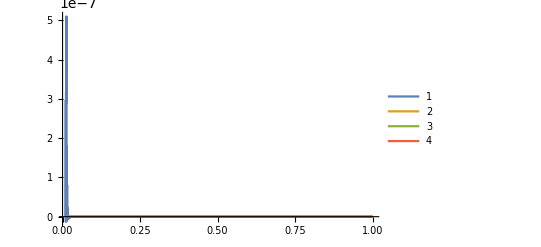

```mathematica
Plot[{(R00[η]-ℛopt[η][[1,1]])/.totBG,(R01[η]-ℛopt[η][[1,2]])/.totBG,(R02[η]-ℛopt[η][[1,3]])/.totBG,(R03[η]-ℛopt[η][[1,4]])/.totBG},{η,ηin,ETA0},PlotRange->All,PlotLegends->Automatic]
```

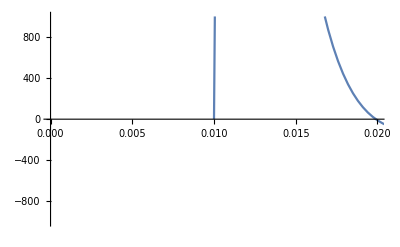

```mathematica
Plot[{(*(R10[η]-ℛopt[η][[2,1]])/.totBG,*)(R11[η]-ℛopt[η][[2,2]])/.totBG(*,(R12[η]-ℛopt[η][[2,3]])/.totBG,(R13[η]-ℛopt[η][[2,4]])/.totBG*)},{η,ηin,ETA0},PlotRange->{{0,0.02},{-1000,1000}},PlotLegends->Automatic]
```

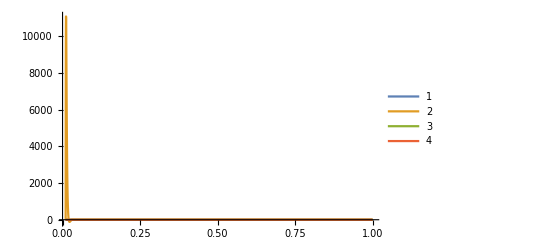

```mathematica
Plot[{(R10[η]-ℛopt[η][[2,1]])/.totBG,(R11[η]-ℛopt[η][[2,2]])/.totBG,(R12[η]-ℛopt[η][[2,3]])/.totBG,(R13[η]-ℛopt[η][[2,4]])/.totBG},{η,ηin,ETA0},PlotRange->All,PlotLegends->Automatic]
```

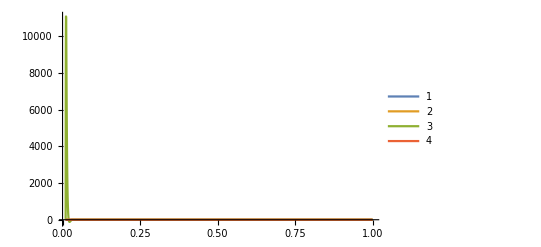

```mathematica
Plot[{(R20[η]-ℛopt[η][[3,1]])/.totBG,(R21[η]-ℛopt[η][[3,2]])/.totBG,(R22[η]-ℛopt[η][[3,3]])/.totBG,(R23[η]-ℛopt[η][[3,4]])/.totBG},{η,ηin,ETA0},PlotRange->All,PlotLegends->Automatic]
```

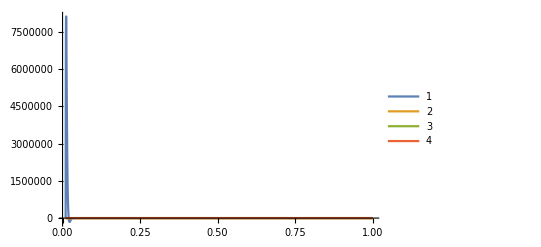

```mathematica
Plot[{(R30[η]-ℛopt[η][[4,1]])/.totBG,(R31[η]-ℛopt[η][[4,2]])/.totBG,(R32[η]-ℛopt[η][[4,3]])/.totBG,(R33[η]-ℛopt[η][[4,4]])/.totBG},{η,ηin,ETA0},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
tmp=Table[τ+ηin,{τ,0,ETA0-ηin,(ETA0-ηin)/100}];
tmp[[Length@tmp]]-ETA0
```

0.

## 𝒲 operators

```mathematica
Mxx={{MXX00,MXX01,MXX02,MXX03},{MXX10,MXX11,MXX12,MXX13},{MXX20,MXX21,MXX22,MXX23},{MXX30,MXX31,MXX32,MXX33}};
Mxl={{MXL00,MXL01,MXL02,MXL03},{MXL10,MXL11,MXL12,MXL13},{MXL20,MXL21,MXL22,MXL23},{MXL30,MXL31,MXL32,MXL33}};
Mlx={{MLX00,MLX01,MLX02,MLX03},{MLX10,MLX11,MLX12,MLX13},{MLX20,MLX21,MLX22,MLX23},{MLX30,MLX31,MLX32,MLX33}};
Mll={{MLL00,MLL01,MLL02,MLL03},{MLL10,MLL11,MLL12,MLL13},{MLL20,MLL21,MLL22,MLL23},{MLL30,MLL31,MLL32,MLL33}};
```

```mathematica
?BGOequations
?SolveBGO
```

BGOequations[W_x,W_y, OPT[t], α[t], E[t], param, t]. Compute the geodesic deviation equations in the parallel transported frame for a group of the Bilocal Geodesic Operators {𝒲_XL,𝒲_LL} and {𝒲_XX,𝒲_LX} in the form {W_x'[t]= α/E W_y[t], W_y'[t]= α/E OPT[t].W_x[t]

SolveBGO[]. Solve the geodesic deviation equations in the parallel transported frame for a group of the Bilocal Geodesic Operators.

### O to S integration of W

```mathematica
Mxleq=BGOequations[Mxl,Mll,ℛll[η],αα[η],EBG[η],param,η];
Mxlgrupbc=Flatten[Table[{Mxl[[i,j]][ETA0]==0,Mll[[i,j]][ETA0]==KroneckerDelta[i,j]},{i,1,Length[Mxl]},{j,1,Length[Mxl]}]];
Timing[Mxlgroupsol=SolveBGO[Mxleq, Mxlgrupbc,Mxl,Mll, totBG, param,η,ηin,ETA0,"SS",60,50,20,10,1000.];]
```

SystemOptions::noset: The value of SystemOption PreemptiveCheckUseThreads cannot be modified.

{26.7582,Null}

```mathematica
Mxxeq=BGOequations[Mxx,Mlx,ℛll[η],αα[η],EBG[η],param,η];
Mxxgrupbc=Flatten[Table[{Mxx[[i,j]][ETA0]==KroneckerDelta[i,j],Mlx[[i,j]][ETA0]==0},{i,1,Length[Mxx]},{j,1,Length[Mxx]}]];
Timing[Mxxgroupsol=SolveBGO[Mxxeq, Mxxgrupbc,Mxx,Mlx, totBG, param,η,ηin,ETA0,"SS",60,50,20,10,1000.];]
```

SystemOptions::noset: The value of SystemOption PreemptiveCheckUseThreads cannot be modified.

{27.7332,Null}

```mathematica
hUU={{0,0,0,1/Q},{0,1,0,0},{0,0,1,0},{1/Q,0,0,1/Q^2}};
hDD={{-1,0,0,Q},{0,1,0,0},{0,0,1,0},{Q,0,0,0}};
hUU.hDD//MatrixForm


functional[η_]:=Flatten[Table[{Mxx[[i,j]]->Mxx[[i,j]][η],Mxl[[i,j]]->Mxl[[i,j]][η],Mlx[[i,j]]->Mlx[[i,j]][η],Mll[[i,j]]->Mll[[i,j]][η]},{i,1,4},{j,1,4}]];
```

(1. | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0. | 0 | 0 | 1.)

```mathematica
BGO=Join[Mxxgroupsol,Mxlgroupsol];
```

```mathematica
MXX[η_]:=Mxx/.functional[η]/.BGO;
MLX[η_]:=Mlx/.functional[η]/.BGO;
MXL[η_]:=Mxl/.functional[η]/.BGO;
MLL[η_]:=Mll/.functional[η]/.BGO;
𝒲[η_]:={{MXX[η],MXL[η]},{MLX[η],MLL[η]}};
```

```mathematica
BGO>>"LCDM_res49999_BGO_bisect.m";
```

```mathematica
𝒲[ηin]//N//MatrixForm

111111111111111111111111111111111111111111111111111111111111111111111111111111111111
𝒲[ETA0]//N//MatrixForm
```

((1. | 0. | 0. | 0.
0. | 0.287739 | 0. | 0.
0. | 0. | 0.287739 | 0.
0.0295667 | 0. | 0. | 1.) | (0.162225 | 0. | 0. | 0.
0. | 0.0607702 | 0. | 0.
0. | 0. | 0.0607702 | 0.
-0.000936098 | 0. | 0. | 0.162225)
(0. | 0. | 0. | 0.
0. | -174.555 | 0. | 0.
0. | 0. | -174.555 | 0.
-2.79797 | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | -33.3905 | 0. | 0.
0. | 0. | -33.3905 | 0.
-0.483466 | 0. | 0. | 1.))

111111111111111111111111111111111111111111111111111111111111111111111111111111111111

((1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.))

### Forward to backwards transformation for 𝒲 operators

In the case when the initial conditions are given at the initial time, i.e. at the source, the BGO are integrated forward in time and they describe the optical properties as seen by the source: to indicate the fact that 𝒲 acts from the source 𝒮 to any point along the null geodesic p_λ, we write 𝒲(p_λ,𝒮). 
However, all observables are “seen” by the observer 𝒪, not by the source! Therefore, before of using these BGO to compute observables they need to be transformed in  𝒲(p_λ,𝒪). This can be done using the BGO properties as described in Grasso & Villa (2021) and in Grasso et. al. (2021).

The procedure to perform the transformations is encoded in this section: note that here we consider that all the quantities (meaning the geodesic and the parallel transported frame) were obtained giving the initial conditions at η_in.

Solve the GDE for BGO forward in time to obtain  𝒲(p_λ,𝒮)

```mathematica
Mxleq=BGOequations[Mxl,Mll,ℛll[η],α[η],EBG[η],param,η];
Mxlgrupbc=Flatten[Table[{Mxl[[i,j]][ηin]==0,Mll[[i,j]][ηin]==KroneckerDelta[i,j]},{i,1,Length[Mxl]},{j,1,Length[Mxl]}]];
Timing[Mxlgroupsol=SolveBGO[Mxleq, Mxlgrupbc,Mxl,Mll, totBG, param,η,ηin,ETA0,"SS",40,prec,10,10,1000.];]
```

SystemOptions::noset: The value of SystemOption PreemptiveCheckUseThreads cannot be modified.

{1872.75,Null}

```mathematica
Mxxeq=BGOequations[Mxx,Mlx,ℛll[η],α[η],EBG[η],param,η];
Mxxgrupbc=Flatten[Table[{Mxx[[i,j]][ηin]==KroneckerDelta[i,j],Mlx[[i,j]][ηin]==0},{i,1,Length[Mxx]},{j,1,Length[Mxx]}]];
Timing[Mxxgroupsol=SolveBGO[Mxxeq, Mxxgrupbc,Mxx,Mlx, totBG, param,η,ηin,ETA0,"SS",40,prec,10,10,1000.];]
```

SystemOptions::noset: The value of SystemOption PreemptiveCheckUseThreads cannot be modified.

{1070.71,Null}

```mathematica
hUU={{0,0,0,1/Q},{0,1,0,0},{0,0,1,0},{1/Q,0,0,1/Q^2}};
hDD={{-1,0,0,Q},{0,1,0,0},{0,0,1,0},{Q,0,0,0}};
hUU.hDD//MatrixForm


functional[η_]:=Flatten[Table[{Mxx[[i,j]]->Mxx[[i,j]][η],Mxl[[i,j]]->Mxl[[i,j]][η],Mlx[[i,j]]->Mlx[[i,j]][η],Mll[[i,j]]->Mll[[i,j]][η]},{i,1,4},{j,1,4}]];
```

(1. | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0. | 0 | 0 | 1.)

```mathematica
BGO=Join[Mxxgroupsol,Mxlgroupsol];
```

The block matrices of 𝒲(p_λ,𝒮) are:

```mathematica
MXX[η_]:=Mxx/.functional[η]/.BGO;
MLX[η_]:=Mlx/.functional[η]/.BGO;
MXL[η_]:=Mxl/.functional[η]/.BGO;
MLL[η_]:=Mll/.functional[η]/.BGO;
ℳ[η_]:={{MXX[η],MXL[η]},{MLX[η],MLL[η]}};
```

Then, 𝒲(p_λ,𝒪) is obtained as:
							𝒲(p_λ,𝒪) = 𝒲(p_λ,𝒮) 𝒲(𝒮,𝒪)
	where 𝒲(𝒮, 𝒪)= 𝒲^-1(𝒪,𝒮).
In other words, we need to compute the inverse of the 8x8 block matrix 𝒲^-1(𝒪,𝒮): this is not a simple task in general but, using the fact that 𝒲 is symplectic, we can find the inverse block components as:

```mathematica
WXX[η_]:=Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mll[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mll[[i,j]]->Mll[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
WLX[η_]:=-Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mlx[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mlx[[i,j]]->Mlx[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
WXL[η_]:=-Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mxl[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mxl[[i,j]]->Mxl[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
WLL[η_]:=Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mxx[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mxx[[i,j]]->Mxx[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
```

Then, the previous components calculated at η_0 give  𝒲^-1(𝒪,𝒮), and finally we have:
							𝒲(p_λ,𝒪) = 𝒲(p_λ,𝒮) 𝒲^-1(𝒪,𝒮)

```mathematica
𝒲[η_]:=({{MXX[η].WXX[ETA0]+MXL[η].WLX[ETA0],MXX[η].WXL[ETA0]+MXL[η].WLL[ETA0]},{MLX[η].WXX[ETA0]+MLL[η].WLX[ETA0],MLX[η].WXL[ETA0]+MLL[η].WLL[ETA0]}})
```

```mathematica
𝒲[ETA0]//N//MatrixForm
ℳ[ηin]//N//MatrixForm
```

((1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
-5.24816×10^-13 | 0. | 0. | 1.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
-5.24816×10^-13 | 0. | 0. | 1.))

((1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.))

```mathematica
BGO>>"FLRWSolver_StoO_res49999_BGO_bisect_0p05.m";
```

```mathematica
𝒲[ηin]//N//MatrixForm
111111111111111111111111111111111111111111111111111111111111111111111111111111111111
𝒲[ETA0]//N//MatrixForm
```

((1. | 0. | 0. | 0.
0. | 0.217925 | 0. | 0.
0. | 0. | 0.217925 | 0.
-0.116937 | 0. | 0. | 1.) | (801.274 | 0. | 0. | 0.
0. | 255.055 | 0. | 0.
0. | 0. | 255.055 | 0.
-51.074 | 0. | 0. | 801.274)
(0. | 0. | 0. | 0.
0. | -0.0380622 | 0. | 0.
0. | 0. | -0.0380622 | 0.
-0.00139256 | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | -39.9585 | 0. | 0.
0. | 0. | -39.9585 | 0.
-0.998882 | 0. | 0. | 1.))

111111111111111111111111111111111111111111111111111111111111111111111111111111111111

((1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
-5.24816×10^-13 | 0. | 0. | 1.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
-5.24816×10^-13 | 0. | 0. | 1.))

## Observables

### Angular diameter distance

```mathematica
tmpWAB=SetPrecision[Table[𝒲[η][[1,2]][[i,j]],{i,2,3},{j,2,3}],prec];
```

```mathematica
detWxlAB[t_]=SetPrecision[Evaluate[Simplify[Sqrt[Abs[(Det[tmpWAB])]]]/.η->t],prec];
```

```mathematica
DangWxl[η_]=Evaluate[(ldown[ETA0].(nup[ETA0]))Evaluate[detWxlAB[η]]/.Join[param,totBG]];
```

```mathematica
DangWxl[ETA0]
```

0.

```mathematica
zbg[η_]:=A[ETA0]/A[η]-1
χz[z_]:=(2 A[ETA0])/𝒽0(Sqrt[z+1]-1)/(z+1)^(3/2)(*A[ETA0]Sqrt[A[ETA0]](1-Sqrt[1/(z+1)])/(z+1)*)(*χz2[z_]:=α[ETA0]Sqrt[α[ETA0]](1-Sqrt[1/(z+1)])/(z+1)*)
```

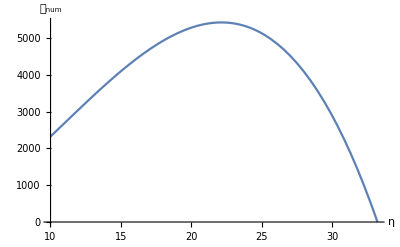

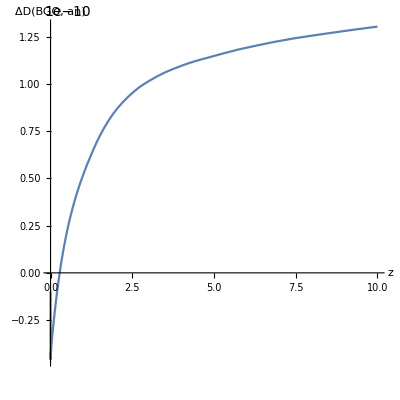

```mathematica
Plot[DangWxl[η],{η,ηin,ETA0},(*WorkingPrecision->10,*)AxesLabel->{"η","𝒟_num"}]

ParametricPlot[{redshift[η],DangWxl[η]/χz[zbg[η]]-1},{η,ηin,ETA0},(*WorkingPrecision->10,*)AxesLabel->{"z","ΔD(BGO, an)"},AspectRatio->1]
```

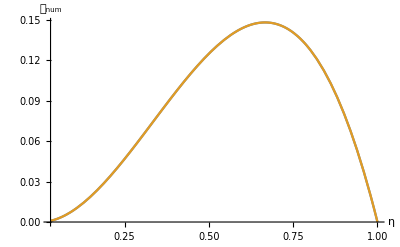

```mathematica
Plot[{DangWxl[η] ,χz[zbg[η]]} ,{η,ηin,ETA0},(*WorkingPrecision->10,*)AxesLabel->{"η","𝒟_num"}]
```

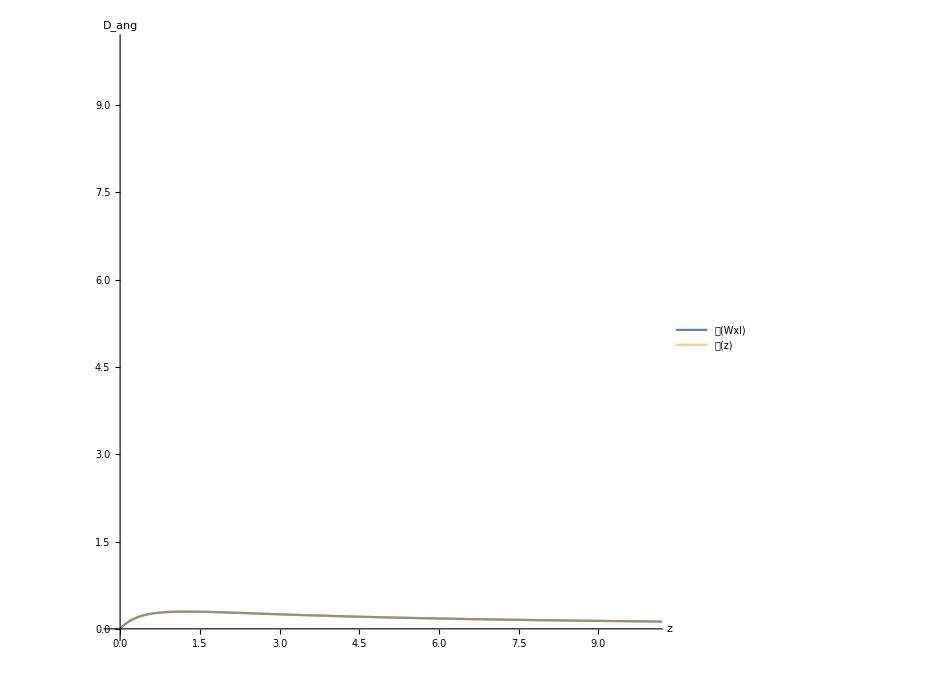

```mathematica
ParametricPlot[{{redshift[η],𝒽0 DangWxl[η]},{redshift[η],𝒽0 χz[redshift[η]]}},{η,ηin,ETA0},PlotRange->{{-0.1,10},{0,10}},PlotStyle->{Thick, Opacity[0.5]},AspectRatio->1,ImageSize->700,PlotLegends->{Style["𝒟(Wxl)",Large],Style["𝒟(z)",Large]},AxesLabel->{Style["z",Large],Style["D_ang",Large]}]
```

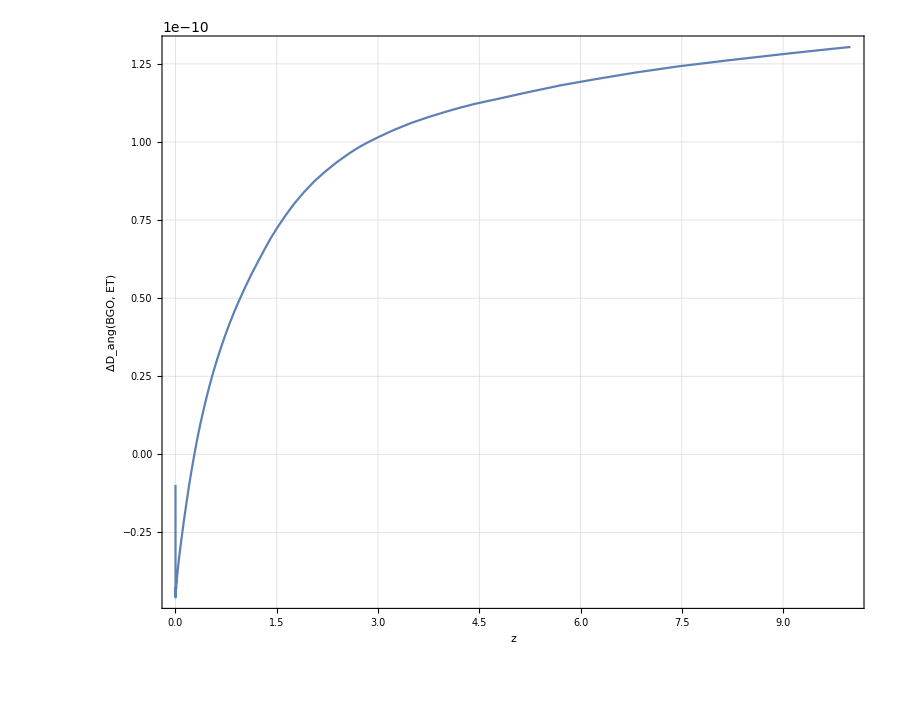

```mathematica
(*{redshift[η], Abs[ (DangWxl2[η]-(χz[redshift[η]]/(1+redshift[η])))/(χz[redshift[η]]/(1+redshift[η]))]}*)
(*LCDMdD=*)
(*znum[η_]:=α[ETA0]/α[η]-1
ParametricPlot[{{redshift[η],  (DangWxl[η]-  χz[zbg[η]])/χz[zbg[η]]},{redshift[η],  (DangWxl[η]-  χz2[znum[η]])/χz2[znum[η]]}},{η,ηin,ETA0},PlotRange->All(*{{0,10},{0,2 10^-23}}*),ImageSize->700,AspectRatio->0.8,Evaluate[StandardPlotStyle[18,24,"ΔD_ang(BGO, an)","z","D_ang in FLRWSolver: numerical vs analytical",{"BGO vs an","BGO vs num"},{0.8,0.8}]]]*)
ParametricPlot[{redshift[η],  (DangWxl[η]-  χz[zbg[η]])/χz[zbg[η]]},{η,ηin,ETA0},PlotRange->All,ImageSize->900,AspectRatio->0.8,Evaluate[StandardPlotStyle[18,24,"ΔD_ang(BGO, ET)","z"," ",{},{}]](*, WorkingPrecision->48*)]
```

### Angular diameter distance, Luminosity distance and Parallax distance

```mathematica
(*𝒲[t_]:=𝒲2[t]*)
```

```mathematica
Timing[tmpWAA=SetPrecision[Table[𝒲[η][[1,1]][[i,j]],{i,2,3},{j,2,3}],prec];]
```

{2.39075,Null}

```mathematica
Timing[detWxxAB[t_]=SetPrecision[Evaluate[Simplify[Sqrt[Abs[(Det[tmpWAA])]]]/.η->t],prec];]
```

{351.036,Null}

```mathematica
(*Uvel[η_]:=Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]/.totBG*)
(*Timing[k[η_]:=Evaluate[EBG[η](nup[η]+Flatten[{0, VV[η]}])]/.totBG;
DangWxl[η_]=Evaluate[(gg4[ETA0].k[ETA0].u[ETA0])Evaluate[detWxlAB[η]]/.Join[param,totBG]];]*)
```

{19.2297,Null}

```mathematica
Dpar[η_]=Evaluate[(ldown[ETA0].(nup[ETA0]))Evaluate[detWxlAB[η]/detWxxAB[η]]/.Join[param,totBG]];
```

```mathematica
DangWxl[ETA0]
Dpar[ETA0]
```

0.

0.

```mathematica
(*redshift[t_]:=((gg4[t].u[t].k[t])/(gg4[ETA0].u[ETA0].k[ETA0])-1)/.Join[totBG,param]*)
```

```mathematica
Dlum[t_]=(1+redshift[t])^2 DangWxl[t];
```

```mathematica
ParametricPlot[{{redshift[t], 𝒽0 DangWxl[t]},{redshift[t],𝒽0 Dlum[t]},{redshift[t],𝒽0 Dpar[t]}} ,{t,ηin,ETA0},WorkingPrecision->30,ImageSize->700,AspectRatio->0.8,PlotRange->{{0,10},{0,1.5}},Evaluate[StandardPlotStyle[18,24,"D/D_ℋ_0","z","Distances in ΛCDM model",{"D_ang","D_lum","D_par"},{1,0.5}]]]
```

-Graphics-

```mathematica
ParametricPlot[{{redshift[t], 𝒽0 DangWxl[t]},{redshift[t],𝒽0 Dlum[t]},{redshift[t],𝒽0 Dpar[t]}} ,{t,ηin,ETA0},WorkingPrecision->30,ImageSize->700,AspectRatio->0.8,PlotRange->{{0,5},{0,15}},Evaluate[StandardPlotStyle[18,24,"D/D_ℋ_0","z","Distances in ΛCDM model",{"D_ang","D_lum","D_par"},{1,0.5}]]]
```

-Graphics-

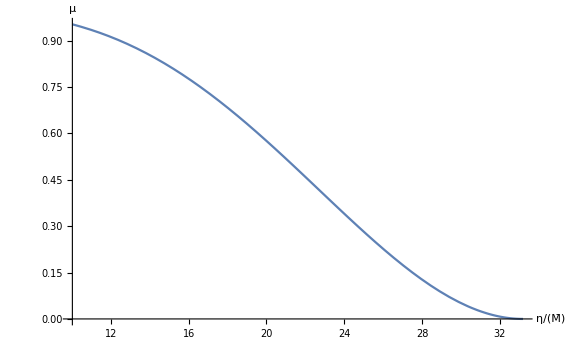

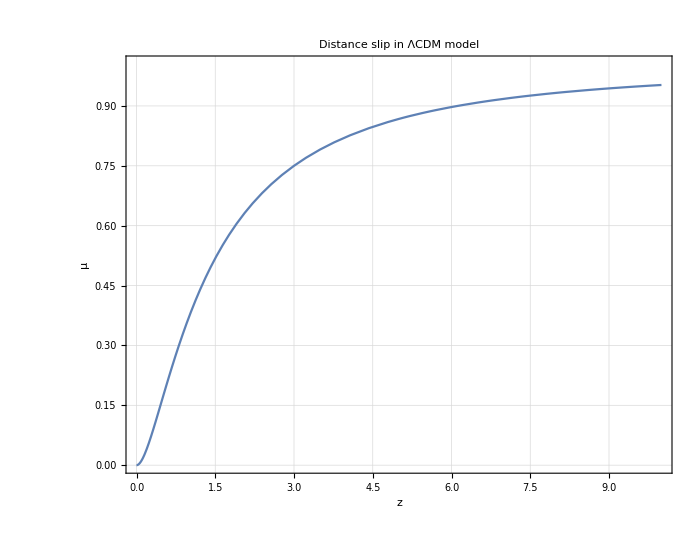

```mathematica
Plot[1-DangWxl[t]^2/Dpar[t]^2 ,{t,ηin,ETA0},WorkingPrecision->30,AxesLabel->{Style["η/(M̄)",Large],Style["μ",Large]},ImageSize->Large]
ParametricPlot[{redshift[t], 1-DangWxl[t]^2/Dpar[t]^2},{t,ηin,ETA0},WorkingPrecision->30,ImageSize->700,AspectRatio->0.8,PlotRange->{{0,10},{0,1.005}},Evaluate[StandardPlotStyle[18,24,"μ","z","Distance slip in ΛCDM model",{ },{ }]]]
```

```mathematica
ADpar[z_]:=A[ETA0]/𝒽0 (Sqrt[1+z]-1)/(3/2 Sqrt[1+z]-1)(*A[ETA0]Sqrt[A[ETA0]] 1/𝒽in (Sqrt[1+z]-1)/(3/2 Sqrt[1+z]-1)*)
```

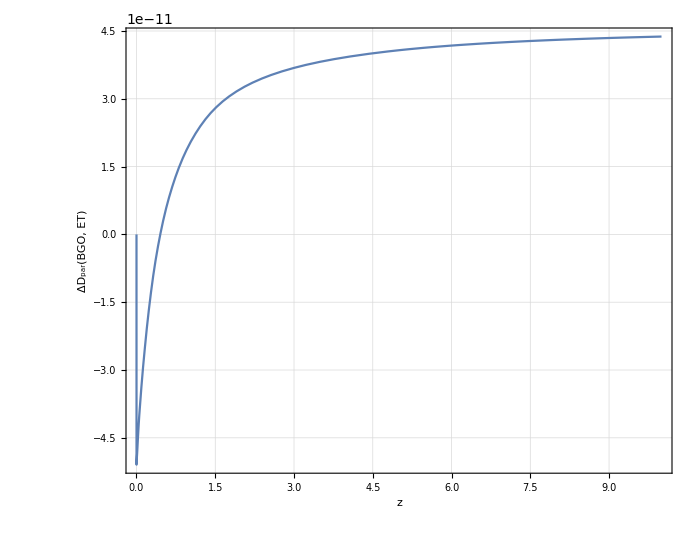

```mathematica
ParametricPlot[{redshift[t], Dpar[t]/ADpar[zbg[t]]-1},{t,ηin,ETA0},WorkingPrecision->30,ImageSize->700,AspectRatio->0.8,PlotRange->All,Evaluate[StandardPlotStyle[18,24,"ΔD_par(BGO, ET)","z"," ",{ },{ }]]]
```

```mathematica
lup[ηin]/.geodesic
{x[ETA0],y[ETA0],z[ETA0]}/.geodesic
```

{-1.,-0.49999999999747,0.5,0.70710678118655}

{11.5944999996104,-11.5944999996691,-16.3970991484669}

```mathematica
Sqrt[2]/2//N
```

0.707107

### Drift effects

```mathematica
hUU={{0,0,0,1/Q},{0,1,0,0},{0,0,1,0},{1/Q,0,0,1/Q^2}};
hDD={{-1,0,0,Q},{0,1,0,0},{0,0,1,0},{Q,0,0,0}};
hUU.hDD//MatrixForm


functional[η_]:=Flatten[Table[{Mxx[[i,j]]->Mxx[[i,j]][η],Mxl[[i,j]]->Mxl[[i,j]][η],Mlx[[i,j]]->Mlx[[i,j]][η],Mll[[i,j]]->Mll[[i,j]][η]},{i,1,4},{j,1,4}]];
```

(1. | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0. | 0 | 0 | 1.)

```mathematica
𝒲XX[η_]=𝒲[η][[1,1]];
𝒲LX[η_]=𝒲[η][[2,1]];
𝒲XL[η_]=𝒲[η][[1,2]];
𝒲LL[η_]=𝒲[η][[2,2]];
IWXL[η_]=Inverse[𝒲XL[η]];
```

```mathematica
IWXL[t].𝒲XL[t]/.t->ηin
```

{{1.,0,0,0},{0,1.,0,0},{0,0,1.,0},{0.,0,0,1.}}

```mathematica
Uoo[η_]:=-hDD.IWXL[η].𝒲XX[η]
Uoe[η_]:=hDD.IWXL[η]
Ueo[η_]:=-(hDD.𝒲LX[η]-hDD.𝒲LL[η].IWXL[η].𝒲XX[η])
Uee[η_]:= -hDD.𝒲LL[η].IWXL[η]
```

```mathematica
𝒰dd[η_]:= {{Uoo[η],Uoe[η]},{Ueo[η],Uee[η]}}
```

```mathematica
(*four acceleration can be calculated as a^ν==u^μ∇_μ u^ν*)
```

```mathematica
𝓊={1/𝒶[η],0,0,0}(*{u0[η],u1[η],u2[η],u3[η]}*);
Table[Sum[(𝓊[[j]]D[𝓊[[i]],X4[[j]]]),{j,1,4}]+Sum[Christoffel[{{-(𝒶[η])^2,0,0,0},{0,(𝒶[η])^2,0,0},{0,0,(𝒶[η])^2,0},{0,0,0,(𝒶[η])^2}},X4][[i,j,s]]𝓊[[j]]𝓊[[s]],{j,1,4},{s,1,4}]//Simplify,{i,1,4}]
```

{0,0,0,0}

```mathematica
e0[s_]=ldown[s]/Q/.geodesic;
e1[η_]=g4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]])/.totBG;
e2[η_]=g4[η].(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]])/.totBG;
e3[η_]=(g4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]])+e0[η])/Q/.totBG;
```

```mathematica
ϕ0[η_]=(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]])/.totBG;
ϕ1[η_]=(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]])/.totBG;
ϕ2[η_]=(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]])/.totBG;
ϕ3[η_]=(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]])/.totBG;
```

```mathematica
up[η_]:={e0[η].u[η],e1[η].u[η],e2[η].u[η],e3[η].u[η]}
lp[η_]:={ϕ0[η].ldown[η],ϕ1[η].ldown[η],ϕ2[η].ldown[η],ϕ3[η].ldown[η]}
```

```mathematica
uE[η_]:={e0[η].u[η],e1[η].u[η],e2[η].u[η],e3[η].u[η]}
aE[η_]:={0,0,0,0}
uO[η_]:={e0[η].u[η],e1[η].u[η],e2[η].u[η],e3[η].u[η]}
aO[η_]:={0,0,0,0}
```

```mathematica
ΞDoppler[η_]:=(lp[η]/(uE[η].lp[η])).(aE[η]/(1+redshift[η]))-(lp[ETA0]/(uO[ETA0].lp[ETA0])).aO[ETA0]
lnzdrift[η_]:=(ΞDoppler[η]-1/(uO[ETA0].lp[ETA0])(Uoo[η].uO[ETA0].uO[ETA0]+1/(1+redshift[η])Uoe[η].uO[ETA0].uE[η]+1/(1+redshift[η])Ueo[η].uE[η].uO[ETA0]+1/(1+redshift[η])^2 Uee[η].uE[η].uE[η]))/.BGO/.geodesic
```

```mathematica
ΞDoppler[t]
```

0

```mathematica
cL=(299792458 3.24078 10^-23)/L(*c/L==(Mpc/s)/Mpc=1/s*)
```

3.62370784236154×10^-17

```mathematica
ANALITICzdrift[t_]:=𝒽0/A[ETA0](1-Sqrt[(1+zbg[t])])/.param
```

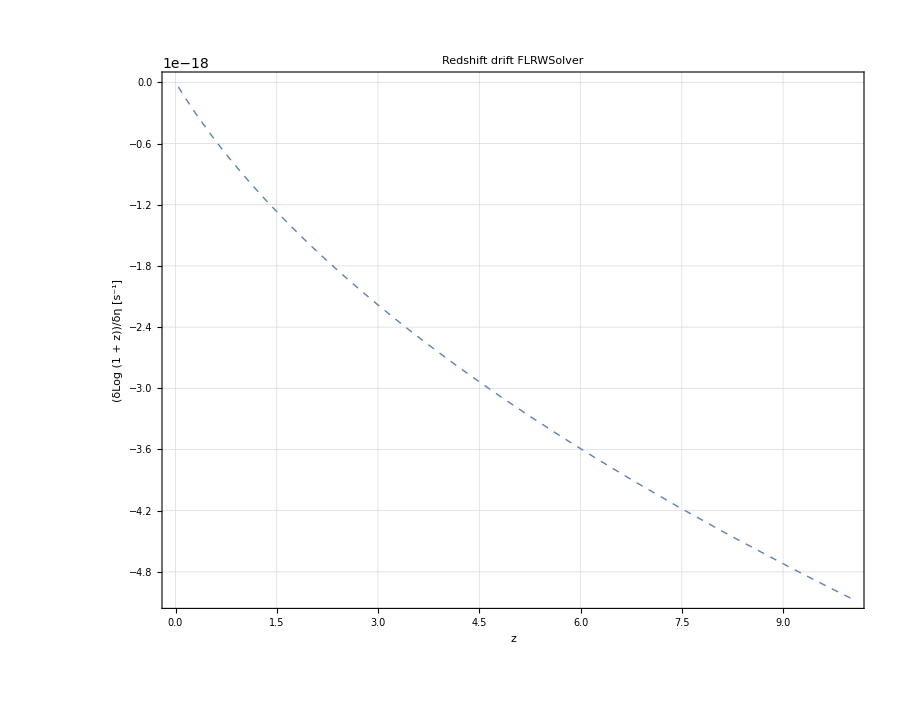

```mathematica
ParametricPlot[{redshift[t],cL ANALITICzdrift[t]},{t,ηin,ETA0},ImageSize->900,PlotRange->All,AspectRatio->0.8,PlotStyle->{Thick,Dashed},Evaluate[StandardPlotStyle[20,24,"(δLog (1 + z))/δη [s^-1]","z","Redshift drift FLRWSolver",{ },{0.8,0.8 }]]]
```

```mathematica
ParametricPlot[{redshift[t],lnzdrift[t]/ANALITICzdrift[t]-1},{t,ηin,ETA0-10^-15},ImageSize->900,PlotRange->{{-0.4,10.4},{-2.5 10^-10,6 10^-10}},AspectRatio->0.8,Evaluate[StandardPlotStyle[20,24,"Δζ(BGO,ET)","z","",{},{}]]]
```

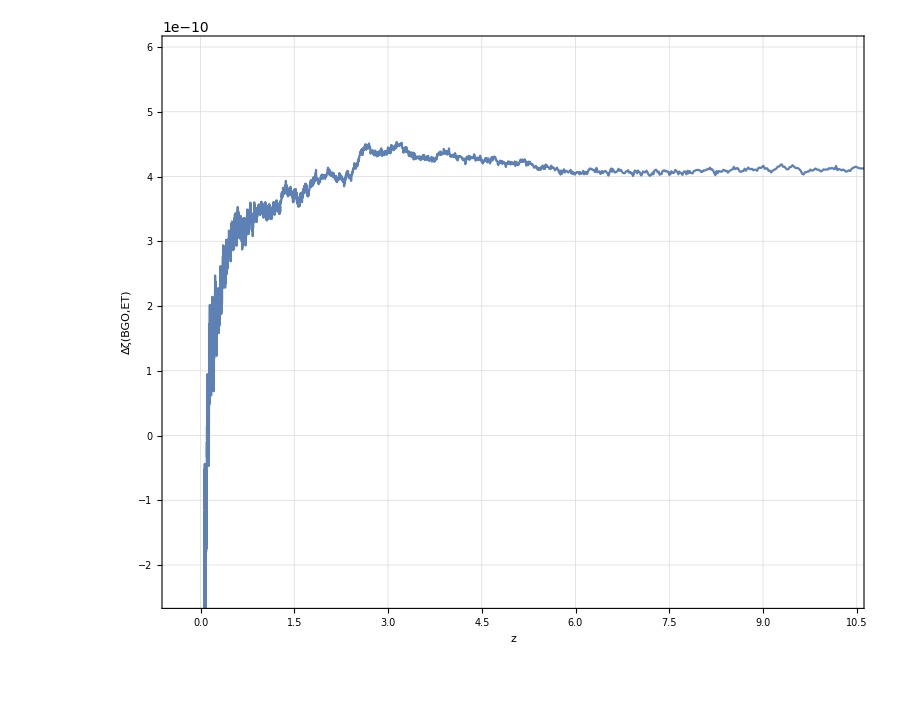

```mathematica
{zFLRWSl->(Evaluate[redshift[#]]&),DangFLRWSl->(Evaluate[DangWxl[#]]&) ,(*DlumLCDM->(Evaluate[Dlum[#]]&) ,*) DparFLRWSl->(Evaluate[Dpar[#]]&) ,ZdriftFLRWSl->(Evaluate[lnzdrift[#]]&) }>>"observables_FLRWSolverN_bisect.m"
```

FILE TOO BOG TO BE SAVED!!!

## Convert BGO to coordinates frame

```mathematica
ϕ0[η_]:=Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]
ϕ1[η_]:=Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]
ϕ2[η_]:=Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]
ϕ3[η_]:=Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]
e0[η_]=ϕ3[η]/Q;
e1[η_]=g4[η].ϕ1[η];
e2[η_]=g4[η].ϕ2[η];
e3[η_]=(g4[η].ϕ0[η]+e0[η])/Q;
```

```mathematica
Φ[η_]:={ϕ0[η],ϕ1[η],ϕ2[η],ϕ3[η]}
Ee[η_]:={e0[η],e1[η],e2[η],e3[η]}
```

```mathematica
McXX[η_]:=Φ[η].Mxx.Ee[η]/.functional[η];
McLX[η_]:=Φ[η].Mlx.Ee[η]/.functional[η];
McXL[η_]:=Φ[η].Mxl.Ee[η]/.functional[η];
McLL[η_]:=Φ[η].Mll.Ee[η]/.functional[η];
```

```mathematica
McXX[t][[1,1]]
```

$Aborted

```mathematica
WXX[η_]:=Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mll[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mll[[i,j]]->Mll[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
WLX[η_]:=-Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mlx[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mlx[[i,j]]->Mlx[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
WXL[η_]:=-Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mxl[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mxl[[i,j]]->Mxl[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
WLL[η_]:=Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mxx[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mxx[[i,j]]->Mxx[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
```

```mathematica
𝒲[η_]:=({{MXX[η].WXX[ETA0]+MXL[η].WLX[ETA0],MXX[η].WXL[ETA0]+MXL[η].WLL[ETA0]},{MLX[η].WXX[ETA0]+MLL[η].WLX[ETA0],MLX[η].WXL[ETA0]+MLL[η].WLL[ETA0]}})
```

```mathematica
𝒲XX[η_]=𝒲[η][[1,1]];
𝒲LX[η_]=𝒲[η][[2,1]];
𝒲XL[η_]=𝒲[η][[1,2]];
𝒲LL[η_]=𝒲[η][[2,2]];
IWXL[η_]=Inverse[𝒲XL[η]];
```

```mathematica
Uoo[η_]:=-h0DD.IWXL[η].𝒲XX[η]
Uoe[η_]:=h0DD.IWXL[η]
Ueo[η_]:=-(h0DD.𝒲LX[η]-h0DD.𝒲LL[η].IWXL[η].𝒲XX[η])
Uee[η_]:= -h0DD.𝒲LL[η].IWXL[η]
```

```mathematica
ΞDoppler[η_]:=(ldown[η]/(uE[η].ldown[η])).(aE[η]/(1+redshift[η]))-(ldown[ETA0]/(uO[ETA0].ldown[ETA0])).aO[ETA0]
lnzdrift[η_]:=(ΞDoppler[η]-1/(uO[ETA0].ldown[ETA0])(Uoo[η].uO[ETA0].uO[ETA0]+1/(1+redshift[η])Uoe[η].uO[ETA0].uE[η]+1/(1+redshift[η])Ueo[η].uE[η].uO[ETA0]+1/(1+redshift[η])^2 Uee[η].uE[η].uE[η]))/.BGO/.geodesic
```

### Shear and expansion

```mathematica
Timing[tmpWllAB=SetPrecision[Table[𝒲[η][[2,2]][[i,j]],{i,2,3},{j,2,3}],50];]
IWxlAB=Inverse[tmpWAB];
```

{748.61,Null}

```mathematica
trxlll[t_]=SetPrecision[Evaluate[Tr[IWxlAB.tmpWllAB]/.η->t],50];
```

```mathematica
DDang[t_]=1/2 DangWxl[t] trxlll[t];
```

```mathematica
𝒮[t_]=Evaluate[(tmpWllAB.IWxlAB)//.η->t];
```

```mathematica
expansion[η_]=Tr[𝒮[η]]/2;
shear[η_]=Sqrt[(Tr[𝒮[η].𝒮[η]]/2-(Tr[𝒮[η]]/2)^2)];
```

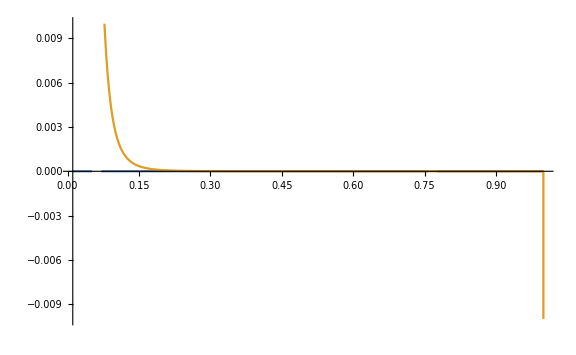

```mathematica
Plot[{shear[η],expansion[η]},{η,ηin,ETA0},ImageSize->Large,PlotRange->0.01]
```

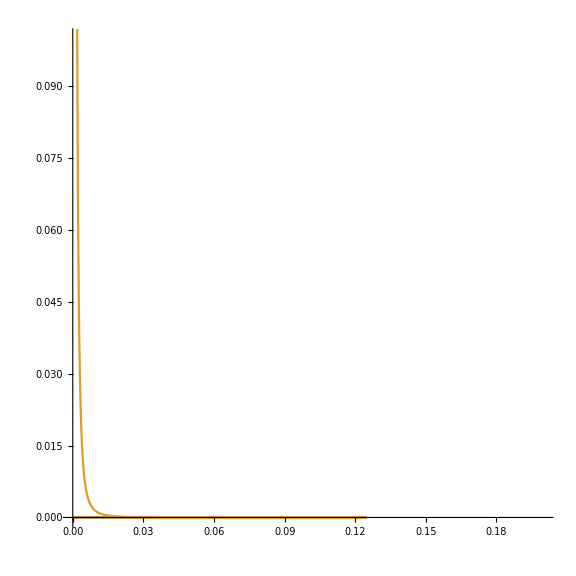

```mathematica
ParametricPlot[{{DangWxl[η], shear[η]},{DangWxl[η],expansion[η]}},{η,ηin,ETA0},ImageSize->Large,PlotRange->{{0,0.2},{0,0.1}}(*{{DangWxl[ETA0], DangWxl[ηin]},{-1,1}}*),AspectRatio->1]
```

```mathematica
δx={0,0,-10^-6/8,-10^-6/8};
δXf[t_]=𝒲[t][[1,2]].δx;
```

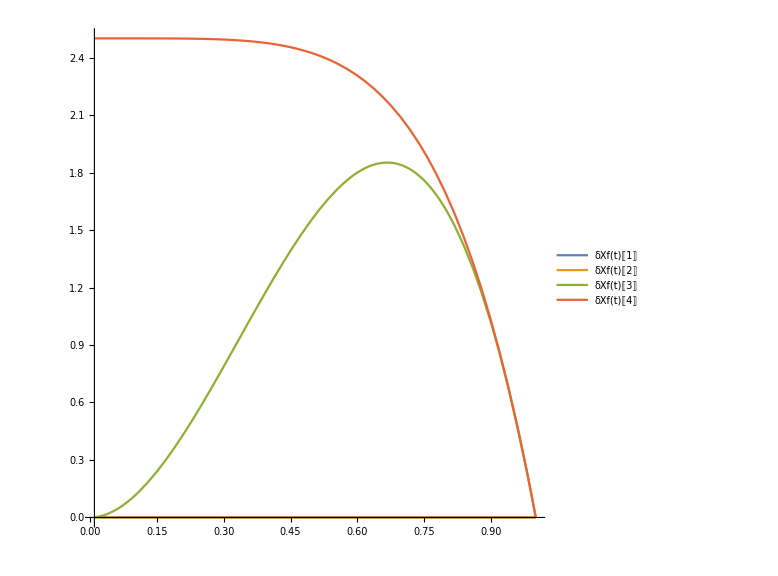

```mathematica
Plot[{δXf[t][[1]],δXf[t][[2]],δXf[t][[3]],δXf[t][[4]]},{t,ηin,ETA0},ImageSize->Large,AspectRatio->1,PlotLegends->"Expressions"]
```

```mathematica
δX0[t_]=(F0[t]/αα[t]).δXf[t]/.Join[param,totBG];
δX1[t_]=(F[t][[1]]-F0[t](ββ[t][[1]])/αα[t]).δXf[t]/.Join[param,totBG];
δX2[t_]=(F[t][[2]]-F0[t](ββ[t][[2]])/αα[t]).δXf[t]/.Join[param,totBG];
δX3[t_]=(F[t][[3]]-F0[t](ββ[t][[3]])/αα[t]).δXf[t]/.Join[param,totBG];
```

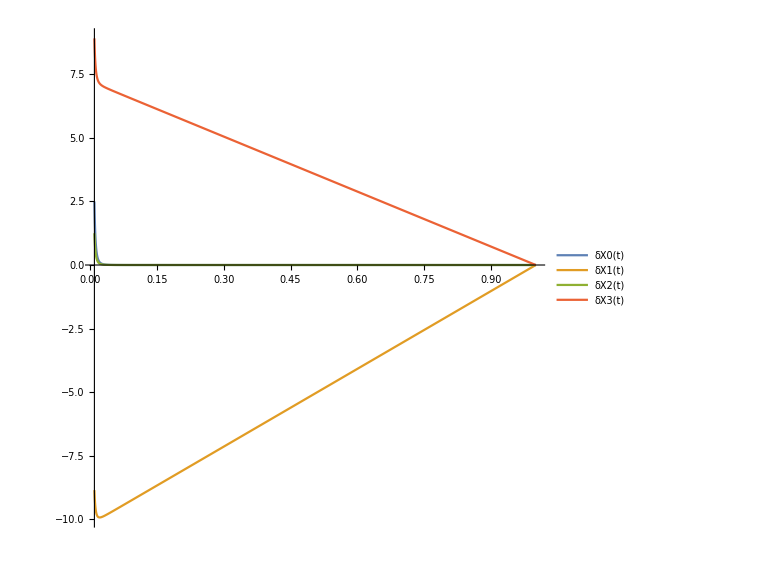

```mathematica
Plot[{δX0[t],δX1[t],δX2[t],δX3[t]},{t,ηin,ETA0},ImageSize->Large,AspectRatio->1,PlotLegends->"Expressions"]
```

```mathematica
Δx[t_]=-{δX0[t],δX1[t],δX2[t],δX3[t]}.ndown[t]/.Join[param,totBG];
ξ[t_]=({δX0[t],δX1[t],δX2[t],δX3[t]}-Δx[t]nup[t])/.Join[param,totBG];
```

```mathematica
Δx[ηin]
ξ[ηin]
```

0.000249999999975000122693

{0,-8.854145189105590659552,1.24999999987500061346,8.912476534011198821003}

```mathematica
δXc[t_]={ξ[t][[2]],ξ[t][[3]],ξ[t][[4]]};
trajectory[t_]=Evaluate[{x[t],y[t],z[t]}/.totBG];
Show[ParametricPlot3D[trajectory[η],{η,ηin,ETA0},PlotRange->{{-1,1},{-1,1},{-1,1}}](*/.Line[x_]:>Sequence[Arrowheads[Table[.02,{100/10}]],Arrow@Line[x]]*) ,Table[Graphics3D[{(*{Opacity[η/300+0.28],Black,Arrowheads[0.02],Arrow[{trajectory[η],(trajectory[η]+40(Pu[η]/.totBG))}]},{Opacity[η/300+0.28],Green,Arrowheads[0.02],Arrow[{trajectory[η],(trajectory[η]+40(P1[η]/.totBG))}]},{Opacity[η/300+0.28],Blue,Arrowheads[0.02],Arrow[{trajectory[η],(trajectory[η]+40(P2[η]/.totBG))}]},{*)(*Opacity[η/300+0.28],*)Red,Arrowheads[0.01],Arrow[{trajectory[η],(trajectory[η]+1/10(δXc[η]/.totBG))}]}],{η,ηin,ETA0,(ETA0-ηin)/30}] , ImageSize->700,AxesLabel->{Style["x/(M̄)",Large],Style["y/(M̄)",Large],Style["z/(M̄)",Large]},AxesStyle->Directive[Black,12],Boxed->False,ViewPoint->{0,100,10}]
```

-Graphics3D-